## Bosons on a Periodic Lattice - Vacuum State

```mathematica
Quit[];
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

First step: Import the GaussianOptimization Package (Run):

```mathematica
Import[NotebookDirectory[]<>"/GaussianOptimization.m"]
```

FT Definitions NEW (Run)

The following definitions are the revised field-theoretic definitions for the covariance matrix. The parameters of the theory are the following:

1. Total number of lattice sites: NN,
2. Mass of the Scalar Field: m,
3. Lattice Spacing: δ,
4. Dimension of subsystems on the lattice: dimA1 & dimB1,
5. Lattice Site Separation between the subsystem partitions: d,
6. Dimension of purifications: dimPur
7. Total length of the circle: L==NNδ . (!  Counting starts at site 0 !)
8. Length of the subsystem: l=(dimA1+dimB1)δ
9. Ratio of subsystem/sistem size: l/L=(dimA1+dimB1)/NN(! Counting starts at site 0 !)
10. Reference State Frequency: μ

The relevant quantities that are calculated from these parameters are the full covariance matrix of the vacuum state of the theory (assuming a small mass m) KGft[{NN,δ,m,μ}], as well as the partial covariance matrix for the subsystem consisting of two sets of lattice sites. These can be set to be adjacent or disjoint, depending on the parameter d (lattice site separation between the subsystems) KGcmRes[NNδmμ,{dimA,dimB,d}].

Notice: In order to account for a non-unit reference state frequency, we simply divide ω by μ in the following:

```mathematica
KGft[{NN_,δ_,m_,μ_}]:=KGft[{NN,δ,m,μ}]={Fourier[Table[(√((m^2+(2/δ Sin[(π k)/NN])^2)/NN))/μ,{k,0,NN-1}]]//Re,Fourier[Table[μ/√(NN(m^2+(2/δ Sin[(π k)/NN])^2)),{k,0,NN-1}]]//Re};
KGb[var_]:=KGb[var]={ToeplitzMatrix[KGft[var]⟦1⟧],ToeplitzMatrix[KGft[var]⟦2⟧]};
KGcm[var_]:=KGcm[var]=ArrayFlatten[{{KGb[var]⟦1⟧,0.},{0.,KGb[var]⟦2⟧}}];(* in qqpp basis *)
KGcmRes[NNδmμ_,{dimA_,dimB_,d_}]:=KGcmRes[NNδmμ,{dimA,dimB,d}]=Module[{ind},
ind=Join[Table[i,{i,dimA}],Table[i+dimA+d,{i,dimB}]];
GOqpqpFROMqqpp[dimA+dimB].ArrayFlatten[{{KGb[NNδmμ]⟦1,ind,ind⟧,0.},{0.,KGb[NNδmμ]⟦2,ind,ind⟧}}].Transpose[GOqpqpFROMqqpp[dimA+dimB]]
](* in qpqp basis *)
```

#### Additional Global Functions:

Functions used for both EoP and CoP:

```mathematica
newM[m_,s_,x_]:=m.GOapproxExp[s,x];
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-10; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 10 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

```mathematica
nb=NotebookDirectory[];
```

```mathematica
Directory[]
nb
```

/Users/HugoCamargo89/Desktop/Projects_AEI/Purifications_Project/Field_Theory

/Users/HugoCamargo89/Desktop/Projects_AEI/Purifications_Project/Field_Theory/

#### Attempt 1 (DON’T RUN)

(*In the following, we assume that dimA1, dimB1, and d are lists of the same length:*)

```mathematica
(*VacCoP[NN_,m_,δ_,μ_,dimA1_,dimB1_,d_]:=Module[{w,TableCM0,rlist,MTra,JT,JR0,function,gradient,ProblemSpecific,LieBasis,M0,M0List,geometry,SystemSpecific,Results={},filename},
SetDirectory[nb];
Import[nb<>"/GaussianOptimization.m"];
w=dimA1;
TableCM0=Table[KGcmRes[{NN,δ,m,μ},{dimA1⟦i⟧,dimB1⟦i⟧,d⟦i⟧}],{i,1,Length[dimA1]}]; 
rlist=Table[Table[GOExtractStdFormG[TableCM0⟦i⟧],{i,1,Length[TableCM0]}]⟦j⟧,{j,1,Length[dimA1]}]⟦All,1⟧;
MTra=Table[Table[GOExtractStdFormG[TableCM0⟦i⟧],{i,1,Length[TableCM0]}]⟦j⟧,{j,1,Length[dimA1]}]⟦All,2⟧;
JT=Table[GOPurifyStandardJBoson[rlist⟦i⟧,(dimA1⟦i⟧+dimB1⟦i⟧),"qpqp"],{i,Length[dimA1]}];
JR0=Table[GOTransformGtoJ[IdentityMatrix[2(2dimA1⟦i⟧+2dimB1⟦i⟧)],"qpqp","qpqp"],{i,Length[dimA1]}]; 
function=Table[GOCoPBos[JT⟦i⟧],{i,Length[dimA1]}]; 
gradient=Table[GOCoPgradBos[JT⟦i⟧],{i,Length[dimA1]}];
ProblemSpecific=Table[{function⟦i⟧,gradient⟦i⟧},{i,Length[dimA1]}];
LieBasis=Table[GOLieBasisCompound[{GOLieBasisEmpty[dimA1⟦i⟧+dimB1⟦i⟧],GOLieBasisSpNoUN[dimA1⟦i⟧+dimB1⟦i⟧]}],{i,Length[dimA1]}];
M0=Table[ArrayFlatten[{{MTra⟦i⟧,0},{0,IdentityMatrix[2(dimA1⟦i⟧+dimB1⟦i⟧)]}}]//SparseArray,{i,Length[dimA1]}];
M0List=Table[Table[MatrixExp[RandomReal[{0,1/10},Length[LieBasis⟦j⟧]].LieBasis⟦j⟧].M0⟦j⟧,{i,1}],{j,Length[dimA1]}];
geometry=Table[GOGeometryConst[LieBasis⟦i⟧,JR0⟦i⟧,+1],{i,Length[dimA1]}];
SystemSpecific=Table[{JR0⟦i⟧,M0List⟦i⟧,LieBasis⟦i⟧,geometry⟦i⟧,newM},{i,Length[dimA1]}];
Table[filename=Directory[]<>"/Data_dw"<>ToString[dimA1]<>".nb";
AppendTo[Results,Append[GOOptimize[ProblemSpecific⟦j⟧,SystemSpecific⟦j⟧,ProcedureSpecific],d⟦j⟧/w⟦j⟧]];
Export[filename,Results,"Data"],{j,1,Length[dimA1]}]]*)
```

```mathematica
(*VacCoP[100,1/100,1/100,1,Table[i,{i,1,10,1}],Table[i,{i,1,10,1}],Table[i,{i,1,10,1}]]*)
```

```mathematica
(*Table[VacCoP[100,1/100,1/100,1,Table[i,{i,1/10,1,1/10}],Table[i,{i,1/10,1,1/10}],α Table[i,{i,1/10,1,1/10}]],{α,{1,2}}]*)
```

```mathematica
(*ParallelTable[VacCoP[NN,m,δ,μ,dimA1,dimB1,d],{α, Join[Table[i,{i,1/10,9/10,1/10}],Table[i,{i,1,10,1/5}]]}]*)
```

#### Version 2 (RUN)

```mathematica
VacCoP[NN_,m_,δ_,μ_,dimA1_,dimB1_,d_]:=Module[{dimPur,CM0,rlist,MTra,JT,JR,J0,M0,function,gradient,ProblemSpecific,LieBasis,M0List,geometry,SystemSpecific,time,Result},
dimPur=dimA1+dimB1;
CM0=KGcmRes[{NN,m,δ,μ},{dimA1,dimB1,d}];
{rlist,MTra}=GOExtractStdFormG[CM0];
JT=GOPurifyStandardJBoson[rlist,dimPur,"qpqp"];
JR=GOTransformGtoJ[IdentityMatrix[2(dimA1+dimB1+dimPur)],"qpqp","qpqp"];
J0=JR;
function=GOCoPBos[JT]; 
gradient=GOCoPgradBos[JT];
ProblemSpecific={function,gradient};
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSpNoUN[dimPur]}];
M0=ArrayFlatten[{{MTra,0},{0,IdentityMatrix[2dimPur]}}]//SparseArray; 
M0List=Table[MatrixExp[RandomReal[{0,7/10},Length[LieBasis]].LieBasis].M0,{i,5}];
geometry=GOGeometryConst[LieBasis,J0,+1];
SystemSpecific={J0,M0List,LieBasis,geometry,newM};
{time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]]];
```

```mathematica
VacEoP[NN_,m_,δ_,μ_,dimA1_,dimB1_,d_,dimA2_,dimB2_]:=Module[{CM0,rlist,MTra,J0,M0,Restriction,function,gradient,ProblemSpecific,LieBasis,M0List,geometry,SystemSpecific,time,Result},
CM0=KGcmRes[{NN,δ,m,μ},{dimA1,dimB1,d}];
{rlist,MTra}=GOExtractStdFormG[CM0];
J0=GOPurifyStandardJBoson[rlist,dimA2+dimB2,"qpqp"];
M0=ArrayFlatten[{{Inverse[MTra],0},{0,IdentityMatrix[2dimA2+2dimB2]}}]//SparseArray;
Restriction=GORestrictionAA[{dimA1,dimB1,dimA2,dimB2}];
function=GOEoPBos[Restriction];
gradient=GOEoPgradBos[Restriction];
ProblemSpecific={function,gradient};
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSp[dimA2+dimB2]}];
M0List=Table[MatrixExp[RandomReal[{0,7/10},Length[LieBasis]].LieBasis].M0,{i,5}];
geometry=GOGeometryConst[LieBasis,J0,+1];
SystemSpecific={J0,M0List,LieBasis,geometry,newM};
{time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]]
];
VacEoP[NN_,m_,δ_,μ_,dimA1_,dimB1_,d_]:=VacEoP[NN,m,δ,μ,dimA1,dimB1,d,dimA1,dimB1];
```

```mathematica
CoPVal[NN_,m_,δ_,μ_,dimA1_,dimB1_,d_]:=VacCoP[NN,m,δ,μ,dimA1,dimB1,d]⟦2⟧⟦1,1⟧;
CoPTime[NN_,m_,δ_,μ_,dimA1_,dimB1_,d_]:=VacCoP[NN,m,δ,μ,dimA1,dimB1,d]⟦1⟧;
EoPVal[NN_,m_,δ_,μ_,dimA1_,dimB1_,d_]:=VacEoP[NN,m,δ,μ,dimA1,dimB1,d]⟦2⟧⟦1,1⟧;
EoPTime[NN_,m_,δ_,μ_,dimA1_,dimB1_,d_]:=VacEoP[NN,m,δ,μ,dimA1,dimB1,d]⟦1⟧;
```

#### Checks that it works (NO need to RUN):

```mathematica
VacCoP[100,1/100,1/100,1,1,1,0]⟦2⟧⟦1,1⟧
VacEoP[100,1/100,1/100,1,1,1,0]⟦2⟧⟦1,1⟧
```

3.64031

2.60131

```mathematica
CoPVal[100,1/100,1/100,1,1,1,0]
CoPTime[100,1/100,1/100,1,1,1,0]
```

3.64031

0.287648

```mathematica
EoPVal[100,1/100,1/100,1,1,1,0]
EoPTime[100,1/100,1/100,1,1,1,0]
```

2.60131

11.347

#### Parameteres and Assumptions:

L=1; (*Length of the circle*)
δ=1/100; (*Lattice spacing*)
m=1/100; (*Mass of the scalar field*)
NN=L/δ; (*Total number of lattice sites*)
μ=1;

dimA1= 1; (*Number of sites in partition A1 of the subsystem*)
dimB1=dimA1; (*Number of sites in partition B1 of the subsystem*) (*Symmetric subsystem paritition*)
dimPur=dimA1+dimB1; (*Minimal Purification - for CoP*)
lA= δ dimA1; (*Length of arc corresponding to subsystem partition A1*)
l = δ(dimA1+dimB1); (*Length of arc corresponding to full subsystem *)
(*d= Table[i,{i,1,10,1}];*) (*# sites separating subsystem partitions A1 & B1 - distance between A1 and B1*)
(*α=d/w;*) (*Ratio between d and w*)
w=dimA1; (*Lattice dimension of subsystem A1*)
d= α w; (* # sites separating subsystem partitions A1 & B1 - distance between A1 and B1 - controlled by α*)
dimA2=dimA1; (*Minimal ancilla for partition A1 - for EoP*)
dimB2=dimB1; (*Minimal ancilla for partition B1 - for EoP*)
(*α=Join[Table[i,{i,1/10,9/10,1/10}],Table[i,{i,1,10,1/5}]];*)

## OLD Calculations

```mathematica
(*CoPVal[NN,m,δ,μ,dimA1,dimB1,d]*)
```

#### 1) l/L=1/100;

```mathematica
CoPListN100dA1=Table[{d,CoPVal[100,1/100,1/100,1,1,1,d]},{d,0,100-(1+1)}];
```

```mathematica
EoPListN100dA1=Table[{d,EoPVal[100,1/100,1/100,1,1,1,d]},{d,0,100-(1+1)}];
```

```mathematica
CoPListN100dA1
```

{{0,3.64031},{1,3.67763},{2,3.67973},{3,3.68037},{4,3.68071},{5,3.68094},{6,3.6811},{7,3.68124},{8,3.68135},{9,3.68145},{10,3.68153},{11,3.68161},{12,3.68167},{13,3.68173},{14,3.68179},{15,3.68184},{16,3.68189},{17,3.68193},{18,3.68197},{19,3.68201},{20,3.68205},{21,3.68208},{22,3.68211},{23,3.68214},{24,3.68216},{25,3.68219},{26,3.68221},{27,3.68224},{28,3.68226},{29,3.68228},{30,3.68229},{31,3.68231},{32,3.68233},{33,3.68234},{34,3.68236},{35,3.68237},{36,3.68238},{37,3.68239},{38,3.6824},{39,3.68241},{40,3.68242},{41,3.68242},{42,3.68243},{43,3.68244},{44,3.68244},{45,3.68244},{46,3.68245},{47,3.68245},{48,3.68245},{49,3.68245},{50,3.68245},{51,3.68245},{52,3.68245},{53,3.68244},{54,3.68244},{55,3.68244},{56,3.68243},{57,3.68242},{58,3.68242},{59,3.68241},{60,3.6824},{61,3.68239},{62,3.68238},{63,3.68237},{64,3.68236},{65,3.68234},{66,3.68233},{67,3.68231},{68,3.68229},{69,3.68228},{70,3.68226},{71,3.68224},{72,3.68221},{73,3.68219},{74,3.68216},{75,3.68214},{76,3.68211},{77,3.68208},{78,3.68205},{79,3.68201},{80,3.68197},{81,3.68193},{82,3.68189},{83,3.68184},{84,3.68179},{85,3.68173},{86,3.68167},{87,3.68161},{88,3.68153},{89,3.68145},{90,3.68135},{91,3.68124},{92,3.6811},{93,3.68094},{94,3.68071},{95,3.68037},{96,3.67973},{97,3.67763},{98,3.64031}}

```mathematica
EoPListN100dA1
```

{{0,2.60131},{1,2.5336},{2,2.4327},{3,2.36804},{4,2.32254},{5,2.2882},{6,2.26102},{7,2.23874},{8,2.22002},{9,2.20398},{10,2.19003},{11,2.17774},{12,2.16681},{13,2.157},{14,2.14815},{15,2.1401},{16,2.13276},{17,2.12603},{18,2.11984},{19,2.11413},{20,2.10885},{21,2.10396},{22,2.09941},{23,2.09519},{24,2.09126},{25,2.08759},{26,2.08418},{27,2.081},{28,2.07804},{29,2.07528},{30,2.07272},{31,2.07033},{32,2.06811},{33,2.06606},{34,2.06416},{35,2.06242},{36,2.06081},{37,2.05934},{38,2.05801},{39,2.0568},{40,2.05572},{41,2.05476},{42,2.05392},{43,2.0532},{44,2.05259},{45,2.05209},{46,2.05171},{47,2.05144},{48,2.05127},{49,2.05122},{50,2.05127},{51,2.05144},{52,2.05171},{53,2.05209},{54,2.05259},{55,2.0532},{56,2.05392},{57,2.05476},{58,2.05572},{59,2.0568},{60,2.05801},{61,2.05934},{62,2.06081},{63,2.06242},{64,2.06416},{65,2.06606},{66,2.06811},{67,2.07033},{68,2.07272},{69,2.07528},{70,2.07804},{71,2.081},{72,2.08418},{73,2.08759},{74,2.09126},{75,2.09519},{76,2.09941},{77,2.10396},{78,2.10885},{79,2.11413},{80,2.11984},{81,2.12603},{82,2.13276},{83,2.1401},{84,2.14815},{85,2.157},{86,2.16681},{87,2.17774},{88,2.19003},{89,2.20398},{90,2.22002},{91,2.23874},{92,2.26102},{93,2.2882},{94,2.32254},{95,2.36804},{96,2.4327},{97,2.5336},{98,2.60131}}

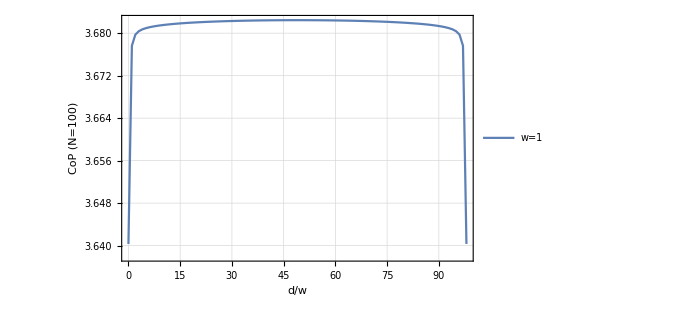

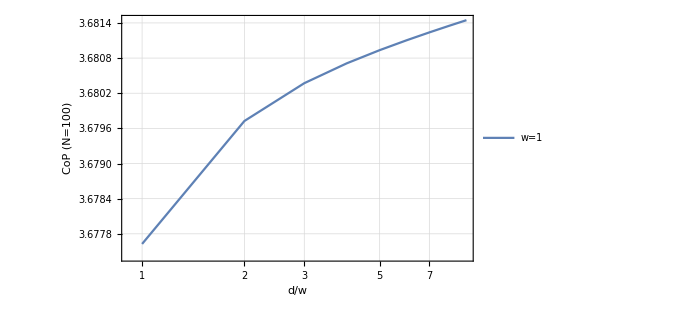

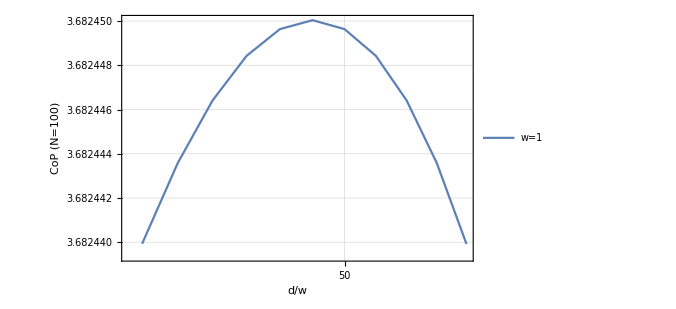

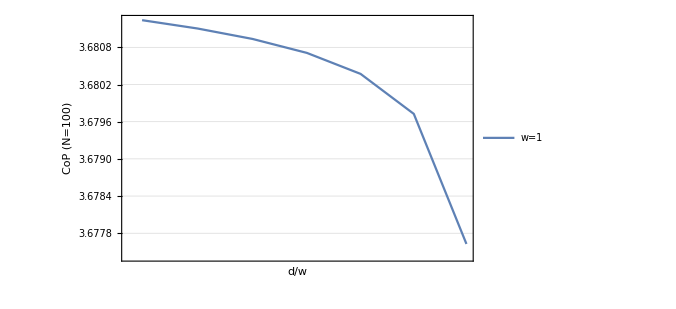

```mathematica
ListPlot[CoPListN100dA1,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "CoP (N=100)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1"}]
ListLogLinearPlot[CoPListN100dA1⟦1;;10⟧,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "CoP (N=100)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1"}]
ListLogLinearPlot[CoPListN100dA1⟦45;;55⟧,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "CoP (N=100)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1"}]
ListLogLinearPlot[CoPListN100dA1⟦92;;98⟧,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "CoP (N=100)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1"}]
```

```mathematica
Normal[NonlinearModelFit[CoPListN100dA1⟦1;;10⟧,a Exp[b x],{a,b},x]]
Normal[LinearModelFit[CoPListN100dA1⟦40;;60⟧,{x},{x}]]
Normal[NonlinearModelFit[CoPListN100dA1⟦92;;98⟧,b-a Log[x],{a,b},x]]
```

3.66543 ⅇ^(0.0006686 x)

3.68244-3.04147×10^-11 x

3.89502-0.0472754 Log[x]

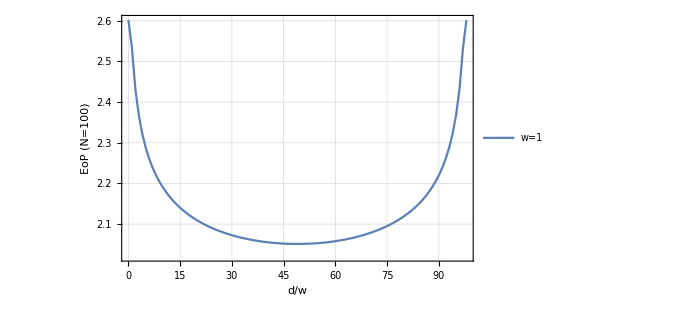

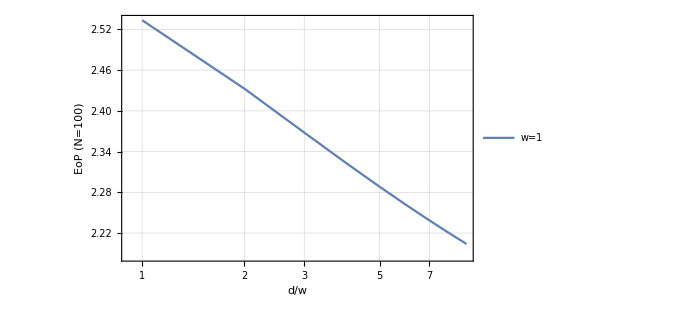

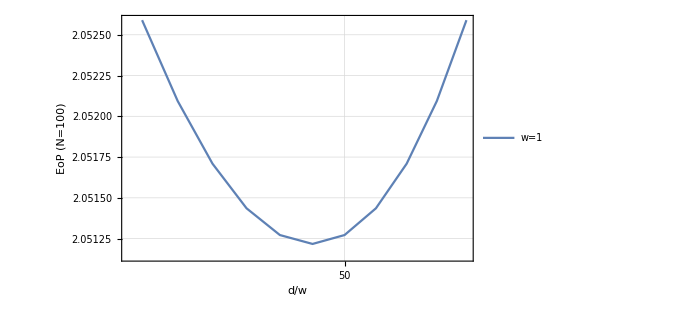

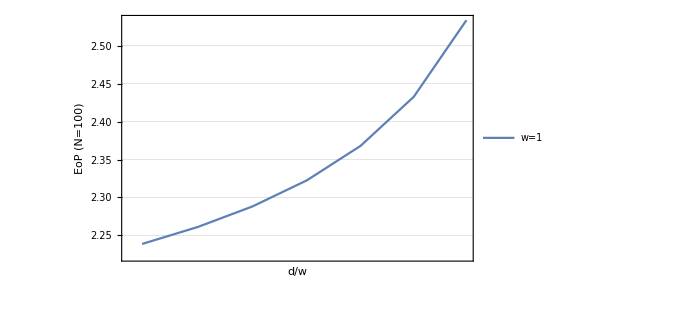

```mathematica
ListPlot[EoPListN100dA1,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "EoP (N=100)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1"}]
ListLogLinearPlot[EoPListN100dA1⟦1;;10⟧,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "EoP (N=100)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1"}]
ListLogLinearPlot[EoPListN100dA1⟦45;;55⟧,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "EoP (N=100)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1"}]
ListLogLinearPlot[EoPListN100dA1⟦92;;98⟧,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "EoP (N=100)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1"}]
```

```mathematica
CoPListN200dA2=Table[{d/2,CoPVal[200,2/100,1/100,1,2,2,d]},{d,0,200-(2+2)}];
```

```mathematica
CoPListN200dA2
```

{{0,4.25711},{1/2,4.30015},{1,4.30342},{3/2,4.3046},{2,4.30527},{5/2,4.30574},{3,4.3061},{7/2,4.3064},{4,4.30665},{9/2,4.30687},{5,4.30706},{11/2,4.30723},{6,4.30739},{13/2,4.30754},{7,4.30767},{15/2,4.30779},{8,4.30791},{17/2,4.30802},{9,4.30812},{19/2,4.30821},{10,4.30831},{21/2,4.30839},{11,4.30847},{23/2,4.30855},{12,4.30862},{25/2,4.30869},{13,4.30876},{27/2,4.30883},{14,4.30889},{29/2,4.30895},{15,4.30901},{31/2,4.30906},{16,4.30911},{33/2,4.30916},{17,4.30921},{35/2,4.30926},{18,4.30931},{37/2,4.30935},{19,4.30939},{39/2,4.30943},{20,4.30947},{41/2,4.30951},{21,4.30955},{43/2,4.30959},{22,4.30962},{45/2,4.30965},{23,4.30969},{47/2,4.30972},{24,4.30975},{49/2,4.30978},{25,4.30981},{51/2,4.30984},{26,4.30986},{53/2,4.30989},{27,4.30991},{55/2,4.30994},{28,4.30996},{57/2,4.30998},{29,4.31001},{59/2,4.31003},{30,4.31005},{61/2,4.31007},{31,4.31009},{63/2,4.31011},{32,4.31012},{65/2,4.31014},{33,4.31016},{67/2,4.31017},{34,4.31019},{69/2,4.3102},{35,4.31022},{71/2,4.31023},{36,4.31025},{73/2,4.31026},{37,4.31027},{75/2,4.31028},{38,4.31029},{77/2,4.3103},{39,4.31031},{79/2,4.31032},{40,4.31033},{81/2,4.31034},{41,4.31035},{83/2,4.31035},{42,4.31036},{85/2,4.31037},{43,4.31037},{87/2,4.31038},{44,4.31038},{89/2,4.31039},{45,4.31039},{91/2,4.3104},{46,4.3104},{93/2,4.3104},{47,4.3104},{95/2,4.3104},{48,4.31041},{97/2,4.31041},{49,4.31041},{99/2,4.31041},{50,4.31041},{101/2,4.3104},{51,4.3104},{103/2,4.3104},{52,4.3104},{105/2,4.3104},{53,4.31039},{107/2,4.31039},{54,4.31038},{109/2,4.31038},{55,4.31037},{111/2,4.31037},{56,4.31036},{113/2,4.31035},{57,4.31035},{115/2,4.31034},{58,4.31033},{117/2,4.31032},{59,4.31031},{119/2,4.3103},{60,4.31029},{121/2,4.31028},{61,4.31027},{123/2,4.31026},{62,4.31025},{125/2,4.31023},{63,4.31022},{127/2,4.3102},{64,4.31019},{129/2,4.31017},{65,4.31016},{131/2,4.31014},{66,4.31012},{133/2,4.31011},{67,4.31009},{135/2,4.31007},{68,4.31005},{137/2,4.31003},{69,4.31001},{139/2,4.30998},{70,4.30996},{141/2,4.30994},{71,4.30991},{143/2,4.30989},{72,4.30986},{145/2,4.30984},{73,4.30981},{147/2,4.30978},{74,4.30975},{149/2,4.30972},{75,4.30969},{151/2,4.30965},{76,4.30962},{153/2,4.30959},{77,4.30955},{155/2,4.30951},{78,4.30947},{157/2,4.30943},{79,4.30939},{159/2,4.30935},{80,4.30931},{161/2,4.30926},{81,4.30921},{163/2,4.30916},{82,4.30911},{165/2,4.30906},{83,4.30901},{167/2,4.30895},{84,4.30889},{169/2,4.30883},{85,4.30876},{171/2,4.30869},{86,4.30862},{173/2,4.30855},{87,4.30847},{175/2,4.30839},{88,4.30831},{177/2,4.30821},{89,4.30812},{179/2,4.30802},{90,4.30791},{181/2,4.30779},{91,4.30767},{183/2,4.30754},{92,4.30739},{185/2,4.30723},{93,4.30706},{187/2,4.30687},{94,4.30665},{189/2,4.3064},{95,4.3061},{191/2,4.30574},{96,4.30527},{193/2,4.3046},{97,4.30342},{195/2,4.30015},{98,4.25711}}

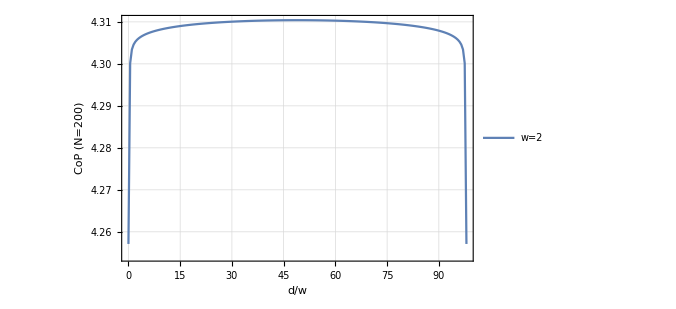

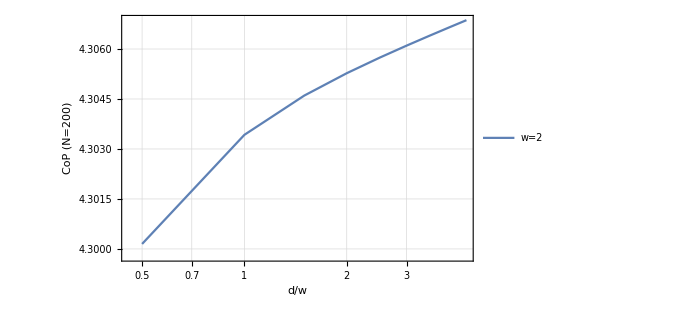

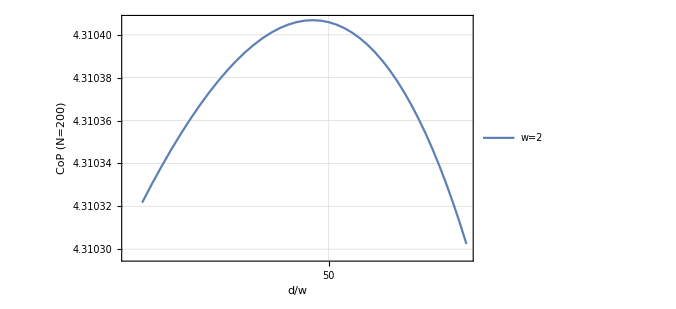

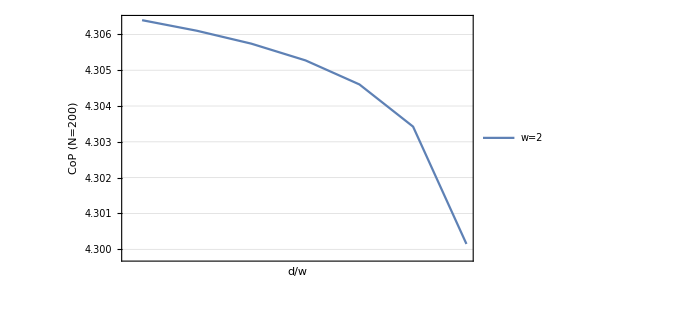

```mathematica
ListPlot[CoPListN200dA2,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "CoP (N=200)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=2"}]
ListLogLinearPlot[CoPListN200dA2⟦1;;10⟧,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "CoP (N=200)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=2"}]
ListLogLinearPlot[CoPListN200dA2⟦80;;120⟧,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "CoP (N=200)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=2"}]
ListLogLinearPlot[CoPListN200dA2⟦190;;196⟧,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "CoP (N=200)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=2"}]
```

```mathematica
Normal[NonlinearModelFit[CoPListN200dA2⟦1;;10⟧,a Exp[b x],{a,b},x]]
Normal[LinearModelFit[CoPListN200dA2⟦80;;120⟧,{x},{x}]]
Normal[NonlinearModelFit[CoPListN200dA2⟦190;;196⟧,b-a Log[x],{a,b},x]]
```

4.28627 ⅇ^(0.00144393 x)

4.31042-9.49987×10^-7 x

5.09262-0.172666 Log[x]

```mathematica
Normal[NonlinearModelFit[CoPListN100dA1⟦1;;10⟧,a Exp[b x],{a,b},x]]
Normal[NonlinearModelFit[CoPListN200dA2⟦1;;20⟧,a Exp[b x],{a,b},x]]
```

3.66543 ⅇ^(0.0006686 x)

4.29483 ⅇ^(0.000446867 x)

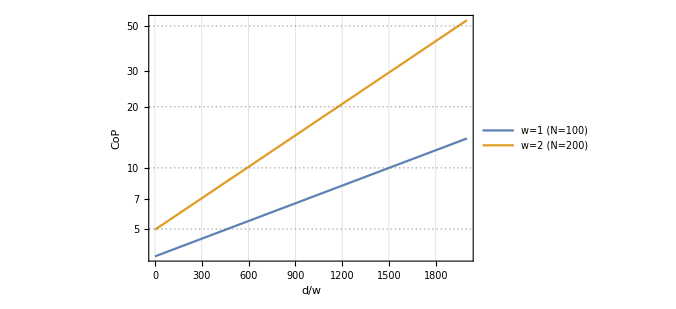

```mathematica
LogPlot[{3.6654308395717785 ⅇ^(0.0006685996165276836 x),4.960726987735741 ⅇ^(0.0011878265110651183 x)},{x,0,2000},PlotTheme->"Detailed",PlotRange->All ,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "CoP"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1 (N=100)","w=2 (N=200)"}]
```

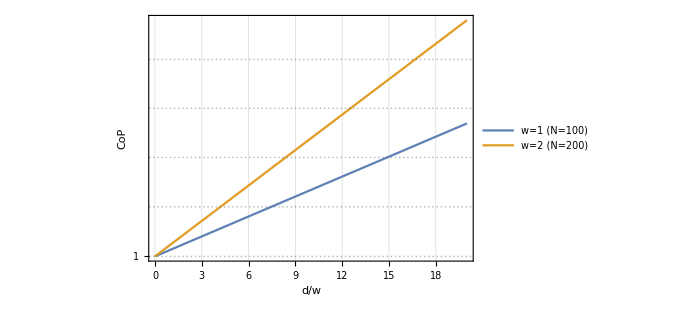

```mathematica
LogPlot[{ⅇ^(0.0006685996165276836 x), ⅇ^(0.0011878265110651183 x)},{x,0,20},PlotTheme->"Detailed",PlotRange->All ,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "CoP"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1 (N=100)","w=2 (N=200)"}]
```

```mathematica
CoPListN100dA1[[50]]
CoPListN200dA2[[100]]
Abs[CoPListN200dA2[[96]][[2]]-CoPListN100dA1[[48]][[2]]]
```

{49,3.68245}

{99/2,4.982}

1.29956

```mathematica
ReglCoPListN200dA2=Join[Table[{CoPListN200dA2[[i,1]]},{i,Length[CoPListN200dA2]}],Table[{(CoPListN200dA2[[i,2]]-Abs[CoPListN200dA2[[96]][[2]]-CoPListN100dA1[[48]][[2]]])},{i,Length[CoPListN200dA2]}],2];
```

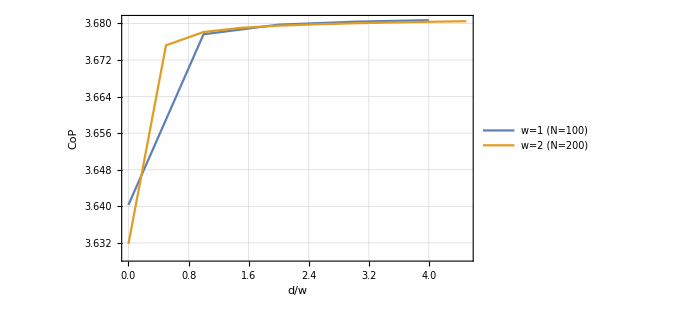

```mathematica
ListPlot[{CoPListN100dA1[[1;;5]],ReglCoPListN200dA2[[1;;10]]},PlotTheme->"Detailed",Joined->True ,PlotRange->All,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "CoP"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1 (N=100)","w=2 (N=200)"}]
```

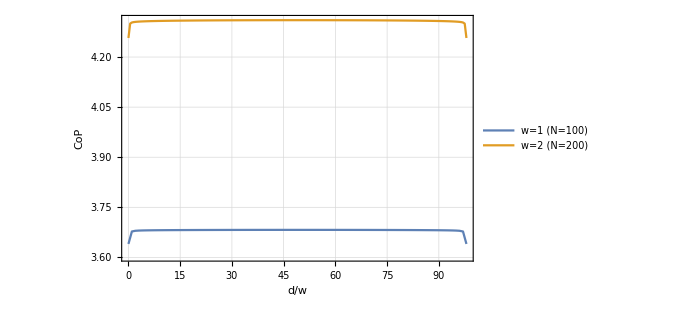

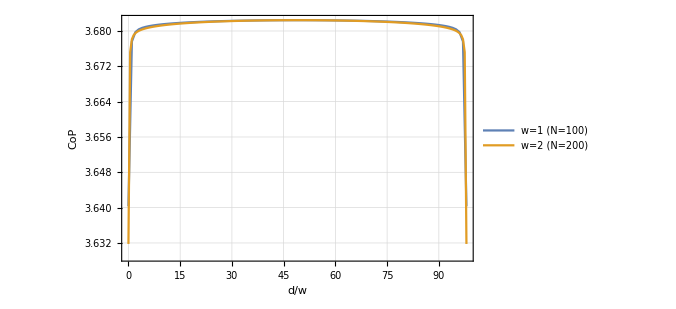

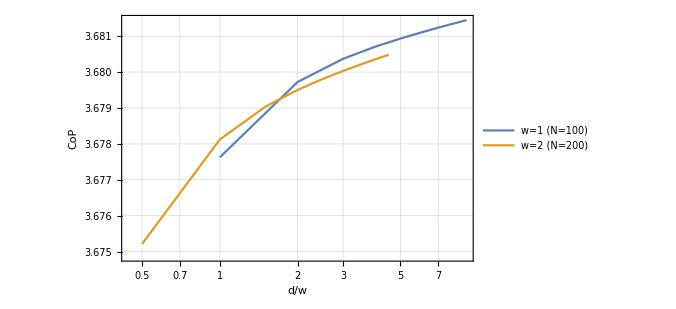

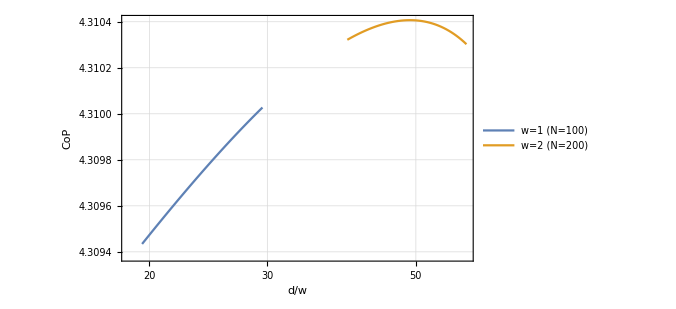

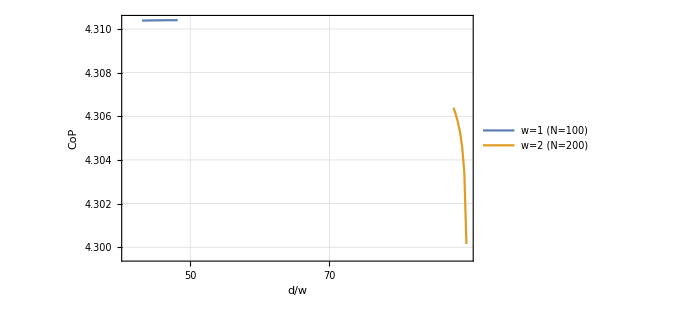

```mathematica
ListPlot[{CoPListN100dA1,CoPListN200dA2},PlotTheme->"Detailed",Joined->True ,PlotRange->All,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "CoP"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1 (N=100)","w=2 (N=200)"}]
ListPlot[{CoPListN100dA1,ReglCoPListN200dA2},PlotTheme->"Detailed",Joined->True ,PlotRange->All,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "CoP"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1 (N=100)","w=2 (N=200)"}]
ListLogLinearPlot[{CoPListN100dA1⟦1;;10⟧,ReglCoPListN200dA2⟦1;;10⟧},PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "CoP"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1 (N=100)","w=2 (N=200)"}]
ListLogLinearPlot[{CoPListN200dA2⟦40;;60⟧,CoPListN200dA2⟦80;;120⟧},PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "CoP"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1 (N=100)","w=2 (N=200)"}]
ListLogLinearPlot[{CoPListN200dA2⟦90;;98⟧,CoPListN200dA2⟦190;;196⟧},PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "CoP"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=1 (N=100)","w=2 (N=200)"}]
```

```mathematica
EoPListN200dA2=Table[{d/2,EoPVal[200,2/100,1/100,1,2,2,d]},{d,0,200-(2+2)}];
```

```mathematica
EoPListN200dA2
```

{{0,2.03649},{1/2,2.02035},{1,1.88475},{3/2,1.81577},{2,1.76714},{5/2,1.72994},{3,1.70007},{7/2,1.67528},{4,1.65422},{9/2,1.63598},{5,1.61995},{11/2,1.60571},{6,1.59293},{13/2,1.58136},{7,1.57082},{15/2,1.56115},{8,1.55224},{17/2,1.54399},{9,1.53632},{19/2,1.52916},{10,1.52246},{21/2,1.51617},{11,1.51025},{23/2,1.50466},{12,1.49938},{25/2,1.49437},{13,1.48962},{27/2,1.48511},{14,1.48081},{29/2,1.47671},{15,1.47279},{31/2,1.46905},{16,1.46547},{33/2,1.46205},{17,1.45876},{35/2,1.45561},{18,1.45259},{37/2,1.44968},{19,1.44689},{39/2,1.4442},{20,1.44161},{41/2,1.43912},{21,1.43672},{43/2,1.43441},{22,1.43218},{45/2,1.43003},{23,1.42796},{47/2,1.42596},{24,1.42403},{49/2,1.42216},{25,1.42036},{51/2,1.41863},{26,1.41695},{53/2,1.41533},{27,1.41377},{55/2,1.41226},{28,1.4108},{57/2,1.4094},{29,1.40804},{59/2,1.40673},{30,1.40547},{61/2,1.40425},{31,1.40308},{63/2,1.40195},{32,1.40086},{65/2,1.39981},{33,1.3988},{67/2,1.39783},{34,1.3969},{69/2,1.39601},{35,1.39515},{71/2,1.39433},{36,1.39354},{73/2,1.39279},{37,1.39207},{75/2,1.39138},{38,1.39073},{77/2,1.39011},{39,1.38952},{79/2,1.38896},{40,1.38844},{81/2,1.38794},{41,1.38747},{83/2,1.38704},{42,1.38663},{85/2,1.38625},{43,1.3859},{87/2,1.38559},{44,1.38529},{89/2,1.38503},{45,1.3848},{91/2,1.38459},{46,1.38441},{93/2,1.38426},{47,1.38414},{95/2,1.38404},{48,1.38397},{97/2,1.38393},{49,1.38392},{99/2,1.38393},{50,1.38397},{101/2,1.38404},{51,1.38414},{103/2,1.38426},{52,1.38441},{105/2,1.38459},{53,1.3848},{107/2,1.38503},{54,1.38529},{109/2,1.38559},{55,1.3859},{111/2,1.38625},{56,1.38663},{113/2,1.38704},{57,1.38747},{115/2,1.38794},{58,1.38844},{117/2,1.38896},{59,1.38952},{119/2,1.39011},{60,1.39073},{121/2,1.39138},{61,1.39207},{123/2,1.39279},{62,1.39354},{125/2,1.39433},{63,1.39515},{127/2,1.39601},{64,1.3969},{129/2,1.39783},{65,1.3988},{131/2,1.39981},{66,1.40086},{133/2,1.40195},{67,1.40308},{135/2,1.40425},{68,1.40547},{137/2,1.40673},{69,1.40804},{139/2,1.4094},{70,1.4108},{141/2,1.41226},{71,1.41377},{143/2,1.41533},{72,1.41695},{145/2,1.41863},{73,1.42036},{147/2,1.42216},{74,1.42403},{149/2,1.42596},{75,1.42796},{151/2,1.43003},{76,1.43218},{153/2,1.43441},{77,1.43672},{155/2,1.43912},{78,1.44161},{157/2,1.4442},{79,1.44689},{159/2,1.44968},{80,1.45259},{161/2,1.45561},{81,1.45876},{163/2,1.46205},{82,1.46547},{165/2,1.46905},{83,1.47279},{167/2,1.47671},{84,1.48081},{169/2,1.48511},{85,1.48962},{171/2,1.49437},{86,1.49938},{173/2,1.50466},{87,1.51025},{175/2,1.51617},{88,1.52246},{177/2,1.52916},{89,1.53632},{179/2,1.54399},{90,1.55224},{181/2,1.56115},{91,1.57082},{183/2,1.58136},{92,1.59293},{185/2,1.60571},{93,1.61995},{187/2,1.63598},{94,1.65422},{189/2,1.67528},{95,1.70007},{191/2,1.72994},{96,1.76714},{193/2,1.81577},{97,1.88475},{195/2,2.02035},{98,2.03649}}

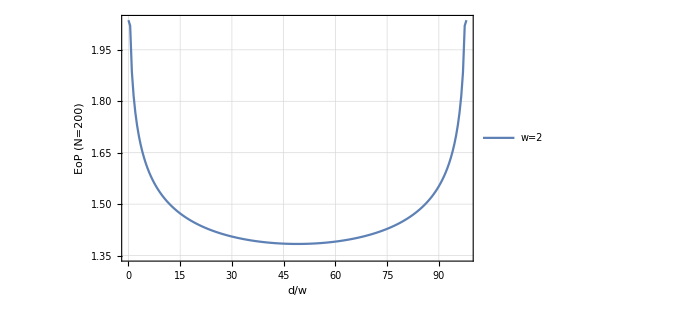

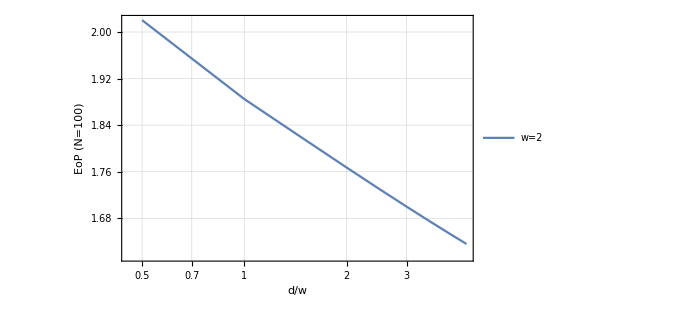

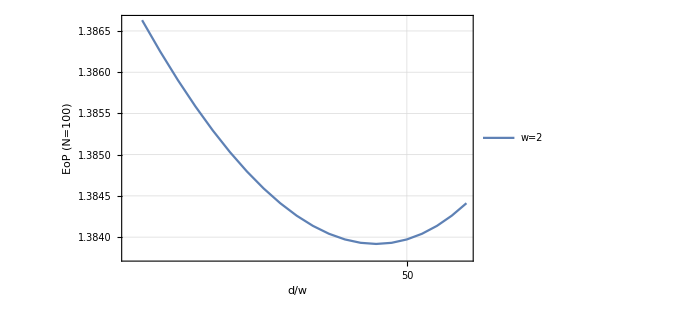

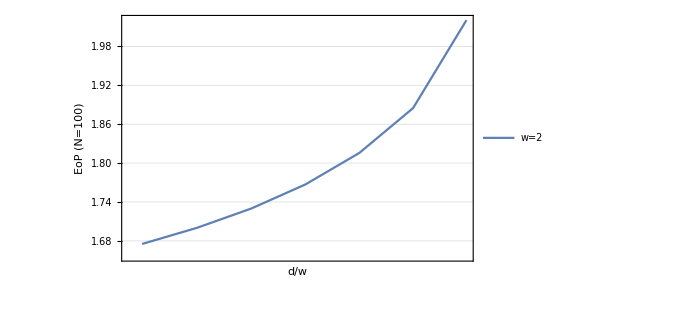

```mathematica
ListPlot[EoPListN200dA2,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "EoP (N=200)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=2"}]
ListLogLinearPlot[EoPListN200dA2⟦1;;10⟧,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "EoP (N=100)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=2"}]
ListLogLinearPlot[EoPListN200dA2⟦85;;105⟧,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "EoP (N=100)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=2"}]
ListLogLinearPlot[EoPListN200dA2⟦190;;196⟧,PlotTheme->"Detailed",Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "EoP (N=100)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{"w=2"}]
```

```mathematica
CoPListN300dA3=Table[{d/3,CoPVal[300,3/100,1/100,1,3,3,d]},{d,3,300-(3+3)}];
```

```mathematica
CoPListN300dA3
```

{{1,4.68144},{4/3,4.68236},{5/3,4.68302},{2,4.68354},{7/3,4.68397},{8/3,4.68434},{3,4.68466},{10/3,4.68495},{11/3,4.68521},{4,4.68545},{13/3,4.68567},{14/3,4.68587},{5,4.68606},{16/3,4.68623},{17/3,4.6864},{6,4.68656},{19/3,4.6867},{20/3,4.68684},{7,4.68697},{22/3,4.6871},{23/3,4.68722},{8,4.68734},{25/3,4.68745},{26/3,4.68755},{9,4.68765},{28/3,4.68775},{29/3,4.68784},{10,4.68793},{31/3,4.68802},{32/3,4.68811},{11,4.68819},{34/3,4.68827},{35/3,4.68834},{12,4.68842},{37/3,4.68849},{38/3,4.68856},{13,4.68862},{40/3,4.68869},{41/3,4.68875},{14,4.68881},{43/3,4.68887},{44/3,4.68893},{15,4.68899},{46/3,4.68905},{47/3,4.6891},{16,4.68915},{49/3,4.6892},{50/3,4.68925},{17,4.6893},{52/3,4.68935},{53/3,4.6894},{18,4.68944},{55/3,4.68949},{56/3,4.68953},{19,4.68957},{58/3,4.68961},{59/3,4.68965},{20,4.68969},{61/3,4.68973},{62/3,4.68977},{21,4.68981},{64/3,4.68984},{65/3,4.68988},{22,4.68991},{67/3,4.68995},{68/3,4.68998},{23,4.69001},{70/3,4.69004},{71/3,4.69007},{24,4.6901},{73/3,4.69013},{74/3,4.69016},{25,4.69019},{76/3,4.69022},{77/3,4.69024},{26,4.69027},{79/3,4.6903},{80/3,4.69032},{27,4.69035},{82/3,4.69037},{83/3,4.6904},{28,4.69042},{85/3,4.69044},{86/3,4.69046},{29,4.69049},{88/3,4.69051},{89/3,4.69053},{30,4.69055},{91/3,4.69057},{92/3,4.69059},{31,4.69061},{94/3,4.69062},{95/3,4.69064},{32,4.69066},{97/3,4.69068},{98/3,4.69069},{33,4.69071},{100/3,4.69073},{101/3,4.69074},{34,4.69076},{103/3,4.69077},{104/3,4.69079},{35,4.6908},{106/3,4.69081},{107/3,4.69083},{36,4.69084},{109/3,4.69085},{110/3,4.69087},{37,4.69088},{112/3,4.69089},{113/3,4.6909},{38,4.69091},{115/3,4.69092},{116/3,4.69093},{39,4.69094},{118/3,4.69095},{119/3,4.69096},{40,4.69097},{121/3,4.69098},{122/3,4.69098},{41,4.69099},{124/3,4.691},{125/3,4.69101},{42,4.69101},{127/3,4.69102},{128/3,4.69102},{43,4.69103},{130/3,4.69104},{131/3,4.69104},{44,4.69105},{133/3,4.69105},{134/3,4.69105},{45,4.69106},{136/3,4.69106},{137/3,4.69106},{46,4.69107},{139/3,4.69107},{140/3,4.69107},{47,4.69107},{142/3,4.69108},{143/3,4.69108},{48,4.69108},{145/3,4.69108},{146/3,4.69108},{49,4.69108},{148/3,4.69108},{149/3,4.69108},{50,4.69108},{151/3,4.69108},{152/3,4.69108},{51,4.69107},{154/3,4.69107},{155/3,4.69107},{52,4.69107},{157/3,4.69106},{158/3,4.69106},{53,4.69106},{160/3,4.69105},{161/3,4.69105},{54,4.69105},{163/3,4.69104},{164/3,4.69104},{55,4.69103},{166/3,4.69102},{167/3,4.69102},{56,4.69101},{169/3,4.69101},{170/3,4.691},{57,4.69099},{172/3,4.69098},{173/3,4.69098},{58,4.69097},{175/3,4.69096},{176/3,4.69095},{59,4.69094},{178/3,4.69093},{179/3,4.69092},{60,4.69091},{181/3,4.6909},{182/3,4.69089},{61,4.69088},{184/3,4.69087},{185/3,4.69085},{62,4.69084},{187/3,4.69083},{188/3,4.69081},{63,4.6908},{190/3,4.69079},{191/3,4.69077},{64,4.69076},{193/3,4.69074},{194/3,4.69073},{65,4.69071},{196/3,4.69069},{197/3,4.69068},{66,4.69066},{199/3,4.69064},{200/3,4.69062},{67,4.69061},{202/3,4.69059},{203/3,4.69057},{68,4.69055},{205/3,4.69053},{206/3,4.69051},{69,4.69049},{208/3,4.69046},{209/3,4.69044},{70,4.69042},{211/3,4.6904},{212/3,4.69037},{71,4.69035},{214/3,4.69032},{215/3,4.6903},{72,4.69027},{217/3,4.69024},{218/3,4.69022},{73,4.69019},{220/3,4.69016},{221/3,4.69013},{74,4.6901},{223/3,4.69007},{224/3,4.69004},{75,4.69001},{226/3,4.68998},{227/3,4.68995},{76,4.68991},{229/3,4.68988},{230/3,4.68984},{77,4.68981},{232/3,4.68977},{233/3,4.68973},{78,4.68969},{235/3,4.68965},{236/3,4.68961},{79,4.68957},{238/3,4.68953},{239/3,4.68949},{80,4.68944},{241/3,4.6894},{242/3,4.68935},{81,4.6893},{244/3,4.68925},{245/3,4.6892},{82,4.68915},{247/3,4.6891},{248/3,4.68905},{83,4.68899},{250/3,4.68893},{251/3,4.68887},{84,4.68881},{253/3,4.68875},{254/3,4.68869},{85,4.68862},{256/3,4.68856},{257/3,4.68849},{86,4.68842},{259/3,4.68834},{260/3,4.68827},{87,4.68819},{262/3,4.68811},{263/3,4.68802},{88,4.68793},{265/3,4.68784},{266/3,4.68775},{89,4.68765},{268/3,4.68755},{269/3,4.68745},{90,4.68734},{271/3,4.68722},{272/3,4.6871},{91,4.68697},{274/3,4.68684},{275/3,4.6867},{92,4.68656},{277/3,4.6864},{278/3,4.68623},{93,4.68606},{280/3,4.68587},{281/3,4.68567},{94,4.68545},{283/3,4.68521},{284/3,4.68495},{95,4.68466},{286/3,4.68434},{287/3,4.68397},{96,4.68354},{289/3,4.68302},{290/3,4.68236},{97,4.68144},{292/3,4.6799},{293/3,4.67604},{98,4.63355}}

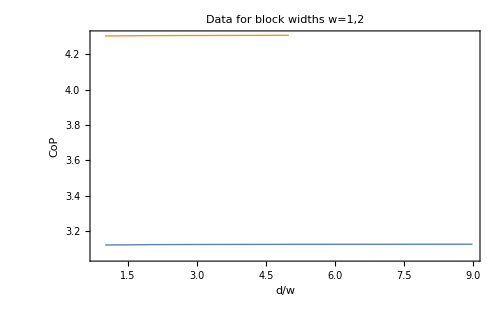

```mathematica
ListPlot[{CoPListN100dA1,CoPListN200dA2},Joined->True,PlotRange->All ,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "CoP"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2"]
```

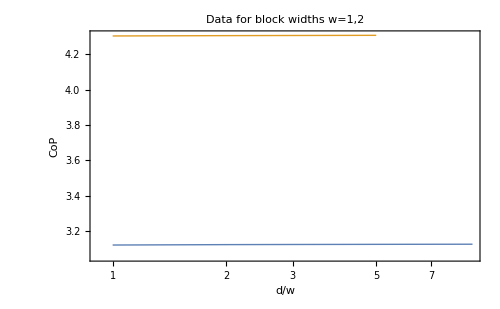

```mathematica
ListLogLinearPlot[{CoPListN100dA1⟦1;;9⟧,CoPListN200dA2⟦1;;9⟧},Joined->True,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "CoP"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2"]
```

```mathematica
(*EoPVal[NN,m,δ,μ,dimA1,dimB1,d]*)
```

```mathematica
EoPListN300dA3=Table[{d/3,EoPVal[300,3/100,1/100,1,3,3,d]},{d,3,300-(3+3)}];
```

```mathematica
EoPListN300dA3
```

{{1,1.50766},{4/3,1.45794},{5/3,1.4197},{2,1.38879},{7/3,1.36297},{8/3,1.3409},{3,1.32169},{10/3,1.30473},{11/3,1.28958},{4,1.27593},{13/3,1.26354},{14/3,1.2522},{5,1.24177},{16/3,1.23212},{17/3,1.22317},{6,1.21481},{19/3,1.207},{20/3,1.19966},{7,1.19275},{22/3,1.18623},{23/3,1.18006},{8,1.17421},{25/3,1.16865},{26/3,1.16335},{9,1.15831},{28/3,1.15348},{29/3,1.14887},{10,1.14446},{31/3,1.14022},{32/3,1.13616},{11,1.13225},{34/3,1.12849},{35/3,1.12487},{12,1.12138},{37/3,1.11801},{38/3,1.11476},{13,1.11162},{40/3,1.10858},{41/3,1.10565},{14,1.1028},{43/3,1.10004},{44/3,1.09737},{15,1.09478},{46/3,1.09227},{47/3,1.08982},{16,1.08745},{49/3,1.08515},{50/3,1.08291},{17,1.08073},{52/3,1.07861},{53/3,1.07655},{18,1.07455},{55/3,1.07259},{56/3,1.07069},{19,1.06883},{58/3,1.06703},{59/3,1.06527},{20,1.06355},{61/3,1.06187},{62/3,1.06024},{21,1.05865},{64/3,1.05709},{65/3,1.05557},{22,1.05409},{67/3,1.05265},{68/3,1.05124},{23,1.04986},{70/3,1.04851},{71/3,1.0472},{24,1.04592},{73/3,1.04466},{74/3,1.04344},{25,1.04224},{76/3,1.04107},{77/3,1.03993},{26,1.03882},{79/3,1.03773},{80/3,1.03666},{27,1.03563},{82/3,1.03461},{83/3,1.03362},{28,1.03265},{85/3,1.0317},{86/3,1.03078},{29,1.02988},{88/3,1.029},{89/3,1.02814},{30,1.0273},{91/3,1.02648},{92/3,1.02568},{31,1.0249},{94/3,1.02414},{95/3,1.02339},{32,1.02267},{97/3,1.02196},{98/3,1.02128},{33,1.0206},{100/3,1.01995},{101/3,1.01932},{34,1.0187},{103/3,1.01809},{104/3,1.01751},{35,1.01694},{106/3,1.01638},{107/3,1.01584},{36,1.01532},{109/3,1.01481},{110/3,1.01432},{37,1.01384},{112/3,1.01338},{113/3,1.01293},{38,1.0125},{115/3,1.01208},{116/3,1.01167},{39,1.01128},{118/3,1.01091},{119/3,1.01054},{40,1.01019},{121/3,1.00986},{122/3,1.00954},{41,1.00923},{124/3,1.00893},{125/3,1.00865},{42,1.00838},{127/3,1.00813},{128/3,1.00788},{43,1.00765},{130/3,1.00744},{131/3,1.00723},{44,1.00704},{133/3,1.00686},{134/3,1.00669},{45,1.00654},{136/3,1.0064},{137/3,1.00627},{46,1.00615},{139/3,1.00605},{140/3,1.00596},{47,1.00588},{142/3,1.00581},{143/3,1.00575},{48,1.00571},{145/3,1.00568},{146/3,1.00566},{49,1.00566},{148/3,1.00566},{149/3,1.00568},{50,1.00571},{151/3,1.00575},{152/3,1.00581},{51,1.00588},{154/3,1.00596},{155/3,1.00605},{52,1.00615},{157/3,1.00627},{158/3,1.0064},{53,1.00654},{160/3,1.00669},{161/3,1.00686},{54,1.00704},{163/3,1.00723},{164/3,1.00744},{55,1.00765},{166/3,1.00788},{167/3,1.00813},{56,1.00838},{169/3,1.00865},{170/3,1.00893},{57,1.00923},{172/3,1.00954},{173/3,1.00986},{58,1.01019},{175/3,1.01054},{176/3,1.01091},{59,1.01128},{178/3,1.01167},{179/3,1.01208},{60,1.0125},{181/3,1.01293},{182/3,1.01338},{61,1.01384},{184/3,1.01432},{185/3,1.01481},{62,1.01532},{187/3,1.01584},{188/3,1.01638},{63,1.01694},{190/3,1.01751},{191/3,1.01809},{64,1.0187},{193/3,1.01932},{194/3,1.01995},{65,1.0206},{196/3,1.02128},{197/3,1.02196},{66,1.02267},{199/3,1.02339},{200/3,1.02414},{67,1.0249},{202/3,1.02568},{203/3,1.02648},{68,1.0273},{205/3,1.02814},{206/3,1.029},{69,1.02988},{208/3,1.03078},{209/3,1.0317},{70,1.03265},{211/3,1.03362},{212/3,1.03461},{71,1.03563},{214/3,1.03666},{215/3,1.03773},{72,1.03882},{217/3,1.03993},{218/3,1.04107},{73,1.04224},{220/3,1.04344},{221/3,1.04466},{74,1.04592},{223/3,1.0472},{224/3,1.04851},{75,1.04986},{226/3,1.05124},{227/3,1.05265},{76,1.05409},{229/3,1.05557},{230/3,1.05709},{77,1.05865},{232/3,1.06024},{233/3,1.06187},{78,1.06355},{235/3,1.06527},{236/3,1.06703},{79,1.06883},{238/3,1.07069},{239/3,1.07259},{80,1.07455},{241/3,1.07655},{242/3,1.07861},{81,1.08073},{244/3,1.08291},{245/3,1.08515},{82,1.08745},{247/3,1.08982},{248/3,1.09227},{83,1.09478},{250/3,1.09737},{251/3,1.10004},{84,1.1028},{253/3,1.10565},{254/3,1.10858},{85,1.11162},{256/3,1.11476},{257/3,1.11801},{86,1.12138},{259/3,1.12487},{260/3,1.12849},{87,1.13225},{262/3,1.13616},{263/3,1.14022},{88,1.14446},{265/3,1.14887},{266/3,1.15348},{89,1.15831},{268/3,1.16335},{269/3,1.16865},{90,1.17421},{271/3,1.18006},{272/3,1.18623},{91,1.19275},{274/3,1.19966},{275/3,1.207},{92,1.21481},{277/3,1.22317},{278/3,1.23212},{93,1.24177},{280/3,1.2522},{281/3,1.26354},{94,1.27593},{283/3,1.28958},{284/3,1.30473},{95,1.32169},{286/3,1.3409},{287/3,1.36297},{96,1.38879},{289/3,1.4197},{290/3,1.45794},{97,1.50766},{292/3,1.57825},{293/3,1.72285},{98,1.725}}

## New Calculations

## Complexity of Purification

### CoP Data

These data sets were obtained by running the commented input on Zero @ AEI.

```mathematica
(*CoPListN100dA1=Table[{d,CoPVal[100,1/100,1/100,1,1,1,d]},{d,0,(100-(1+1))/2}]*)
```

```mathematica
CoPListN100dA1={{0,3.640315804781124},{1,3.677627033925028},{2,3.6797260548746866},{3,3.680371188959455},{4,3.680710148509393},{5,3.6809352587814788},{6,3.681103586292271},{7,3.6812382305650577},{8,3.681350560669364},{9,3.681446951477339},{10,3.681531330002338},{11,3.6816062942524557},{12,3.6816736290586647},{13,3.681734658542095},{14,3.681790356126732},{15,3.6818414753170043},{16,3.6818886087225935},{17,3.6819322310711757},{18,3.6819727313191346},{19,3.682010424104942},{20,3.68204557947238},{21,3.682078422878344},{22,3.682109145246019},{23,3.682137910920508},{24,3.682164863119715},{25,3.682190122293376},{26,3.6822137994479363},{27,3.682235988299231},{28,3.6822567726536497},{29,3.6822762278872845},{30,3.6822944144232235},{31,3.6823113977500084},{32,3.68232722342413},{33,3.682341942299204},{34,3.682355594702527},{35,3.6823682175464056},{36,3.682379844068008},{37,3.682390504270999},{38,3.6824002230863155},{39,3.6824090258098656},{40,3.6824169313589805},{41,3.6824239594036148},{42,3.6824301252577123},{43,3.6824354412966382},{44,3.682439921029486},{45,3.6824435760501677},{46,3.682446406402046},{47,3.682448425311343},{48,3.6824496351209235},{49,3.6824500381947556}};
```

```mathematica
(*CoPListN200dA2=Table[{d/2,CoPVal[200,2/100,1/100,1,2,2,d]},{d,0,(200-(2+2))/2}]*)
```

```mathematica
CoPListN200dA2={{0,4.257111232015298},{1/2,4.300149449516557},{1,4.303424837153722},{3/2,4.3046023147166785},{2,4.305273320645756},{5/2,4.30574073056773},{3,4.306101408276688},{7/2,4.306396564324626},{4,4.306647216405919},{9/2,4.3068654947536285},{5,4.307059048230293},{11/2,4.3072330240218095},{6,4.307391064808264},{13/2,4.307535850402842},{7,4.307669414622534},{15/2,4.3077933406263025},{8,4.307908887425628},{17/2,4.308017073718057},{9,4.308118736536378},{19/2,4.308214572348724},{10,4.308305167990768},{21/2,4.308391022434779},{11,4.3084725626050995},{23/2,4.308550159070542},{12,4.308624133537754},{25/2,4.308694768235184},{13,4.3087623118951255},{27/2,4.308826984994197},{14,4.308888983660567},{29/2,4.308948483395476},{15,4.309005641448279},{31/2,4.309060600347463},{16,4.309113488283754},{33/2,4.309164421626306},{17,4.309213506629123},{35/2,4.309260839736012},{18,4.309306510441987},{37/2,4.309350599201365},{19,4.309393180919269},{39/2,4.309434324350533},{20,4.309474093567908},{41/2,4.30951254746647},{21,4.309549740014866},{43/2,4.309585722047121},{22,4.3096205405721095},{45/2,4.309654239967068},{23,4.309686860765891},{47/2,4.309718441131045},{24,4.30974901676151},{49/2,4.3097786212059646},{25,4.309807285908825},{51/2,4.309835039971485},{26,4.309861911695091},{53/2,4.309887926400547},{27,4.309913108734428},{55/2,4.309937481709903},{28,4.3099610669838055},{57/2,4.309983885031387},{29,4.310005954885263},{59/2,4.31002729542999},{30,4.3100479236041895},{61/2,4.310067855046557},{31,4.310087105981882},{63/2,4.310105690629588},{32,4.310123622462513},{65/2,4.3101409148691605},{33,4.310157579555002},{67/2,4.310173629227664},{34,4.3101890740010385},{69/2,4.3102039242359345},{35,4.310218190751147},{71/2,4.310231882009767},{36,4.310245006954487},{73/2,4.310257574121703},{37,4.310269591154083},{75/2,4.310281065597599},{38,4.310292004601679},{77/2,4.310302414466884},{39,4.310312301619252},{79/2,4.3103216717108115},{40,4.310330529944824},{81/2,4.310338882428066},{41,4.310346732913612},{83/2,4.310354086192812},{42,4.3103609466112},{85/2,4.3103673176212665},{43,4.31037320295373},{87/2,4.3103786058658065},{44,4.310383529195787},{89/2,4.310387975488069},{45,4.3103919478936215},{91/2,4.310395447549969},{46,4.310398477186761},{93/2,4.310401037854552},{47,4.310403131107564},{95/2,4.310404757793731},{48,4.31040591945934},{97/2,4.310406615796792},{49,4.310406848232987}};
```

```mathematica
(*CoPListN300dA3=Table[{d/3,CoPVal[300,3/100,1/100,1,3,3,d]},{d,0,(300-(3+3))/2}]*)
```

```mathematica
CoPListN300dA3={{0,4.633550304700523},{1/3,4.676037089382261},{2/3,4.679898392175942},{1,4.68143512983065},{4/3,4.682357980931667},{5/3,4.683019863194436},{2,4.683539911910852},{7/3,4.683970726955673},{8/3,4.6843398558422},{3,4.684663517483311},{10/3,4.684952098991013},{11/3,4.685212681915735},{4,4.685450330224805},{13/3,4.685668803663183},{14/3,4.685870978348856},{5,4.686059108842294},{16/3,4.6862349987008765},{17/3,4.686400115475003},{6,4.686555670888071},{19/3,4.686702677831055},{20/3,4.6868419925613045},{7,4.686974345654414},{22/3,4.687100365930975},{23/3,4.687220598684376},{8,4.687335520212526},{25/3,4.687445548772689},{26/3,4.68755105392053},{9,4.687652363977471},{28/3,4.687749771821479},{29/3,4.6878435397544616},{10,4.687933904033008},{31/3,4.68802107768822},{32/3,4.688105254020962},{11,4.688186608589334},{34/3,4.68826530140173},{35/3,4.688341478934672},{12,4.688415275305853},{37/3,4.688486813760052},{38/3,4.688556207984474},{13,4.688623562729085},{40/3,4.688688975046158},{41/3,4.688752534728152},{14,4.688814325256833},{43/3,4.688874424260522},{44/3,4.688932904085287},{15,4.688989832280866},{46/3,4.689045271933977},{47/3,4.6890992820804005},{16,4.689151918173528},{49/3,4.6892032320353545},{50/3,4.68925327259745},{17,4.689302085801469},{52/3,4.689349714967154},{53/3,4.689396200804402},{18,4.6894415819350925},{55/3,4.6894858948365},{56/3,4.689529173879221},{19,4.689571451676212},{58/3,4.689612759202305},{59/3,4.689653125673892},{20,4.6896925790852295},{61/3,4.6897311457352},{62/3,4.689768850843061},{21,4.689805718364992},{64/3,4.689841771073791},{65/3,4.689877030612301},{22,4.689911517739327},{67/3,4.689945252230316},{68/3,4.689978252864699},{23,4.6900105377395995},{70/3,4.690042124022853},{71/3,4.690073028233375},{24,4.690103265995339},{73/3,4.690132852556277},{74/3,4.690161802302497},{25,4.690190129016013},{76/3,4.690217845977747},{77/3,4.690244965975747},{26,4.69027150120757},{79/3,4.69029746334295},{80/3,4.690322863648779},{27,4.690347712993161},{82/3,4.6903720216810765},{83/3,4.690395799712412},{28,4.6904190566659185},{85/3,4.690441801879256},{86/3,4.690464044090914},{29,4.690485791883906},{88/3,4.6905070535426985},{89/3,4.690527836958609},{30,4.6905481496737504},{91/3,4.690567999048201},{92/3,4.690587392185506},{31,4.69060633592184},{94/3,4.690624836783108},{95/3,4.690642901093581},{32,4.690660534883951},{97/3,4.690677744110603},{98/3,4.690694534349936},{33,4.690710911101957},{100/3,4.690726879627297},{101/3,4.690742444969923},{34,4.690757611980308},{103/3,4.690772385391237},{104/3,4.690786769713492},{35,4.690800769339156},{106/3,4.690814388465946},{107/3,4.69082763110965},{36,4.690840501204544},{109/3,4.690853002494126},{110/3,4.6908651385759095},{37,4.690876912933808},{112/3,4.690888328910518},{113/3,4.690899389820313},{38,4.6909100985276515},{115/3,4.690920458173094},{116/3,4.690930471570306},{39,4.690940141422698},{118/3,4.690949470419492},{119/3,4.690958460936238},{40,4.6909671155332315},{121/3,4.690975436427512},{122/3,4.6909834258121865},{41,4.690991085791344},{124/3,4.690998418412182},{125/3,4.691005425480601},{42,4.691012108841974},{127/3,4.6910184702803885},{128/3,4.69102451136122},{43,4.69103023362538},{130/3,4.69103563849843},{131/3,4.691040727427754},{44,4.6910455016256725},{133/3,4.691049962300222},{134/3,4.691054110604294},{45,4.691057947509968},{136/3,4.691061473982976},{137/3,4.691064690932436},{46,4.69106759912323},{139/3,4.6910701992528425},{140/3,4.691072492060188},{47,4.691074477978704},{142/3,4.691076157556989},{143/3,4.691077531178965},{48,4.6910785991888755},{145/3,4.6910793619510605},{146/3,4.691079819453739},{49,4.691079971932457}};
```

```mathematica
(*CoPListN400dA4=Table[{d/4,CoPVal[400,4/100,1/100,1,4,4,d]},{d,0,(400-(4+4))/2}]*)
```

```mathematica
CoPListN400dA4={{0,4.8982768935630805},{1/4,4.938816532780222},{1/2,4.942970070770792},{3/4,4.944747338395683},{1,4.945856408555552},{5/4,4.9466691380194705},{3/2,4.947316157303218},{7/4,4.947856847337155},{2,4.94832298480537},{9/4,4.9487335874207785},{5/2,4.9491009910065795},{11/4,4.949433692226232},{3,4.949737818792399},{13/4,4.950017952611518},{7/2,4.950277620130216},{15/4,4.950519600565081},{4,4.9507461275659335},{17/4,4.9509590261418355},{9/2,4.95115980867592},{19/4,4.951349743737828},{5,4.951529906730782},{21/4,4.951701217840827},{11/2,4.951864471117281},{23/4,4.952020356586747},{6,4.952169478067404},{25/4,4.9523123670231195},{13/2,4.952449493889873},{27/4,4.952581277059154},{7,4.952708090365587},{29/4,4.952830269328458},{15/2,4.952948116120959},{31/4,4.953061904005507},{8,4.9531718807088865},{33/4,4.953278271851763},{17/2,4.953381283137945},{35/4,4.953481102975735},{9,4.953577904108753},{37/4,4.953671845521419},{19/2,4.9537630736078},{39/4,4.953851723816465},{10,4.953937921301665},{41/4,4.954021782319913},{21/2,4.954103414816933},{43/4,4.954182919260566},{11,4.954260389371925},{45/4,4.954335912677049},{23/2,4.954409570873934},{47/4,4.954481440762059},{12,4.954551594090037},{49/4,4.954620098479641},{25/2,4.954687017315179},{51/4,4.954752410428249},{13,4.954816334070592},{53/4,4.954878841464107},{27/2,4.954939982814674},{55/4,4.954999805551386},{14,4.955058354644283},{57/4,4.95511567266774},{29/2,4.955171800043543},{59/4,4.955226775030908},{15,4.955280634073593},{61/4,4.955333411809797},{31/2,4.955385141167738},{63/4,4.955435853454591},{16,4.955485578700273},{65/4,4.955534345253633},{33/2,4.955582180443382},{67/4,4.955629110227609},{17,4.955675159428879},{69/4,4.955720351773144},{35/2,4.955764710020474},{71/4,4.955808255891284},{18,4.955851010227146},{73/4,4.955892992999561},{37/2,4.955934223392379},{75/4,4.9559747197220645},{19,4.956014499710887},{77/4,4.956053580253796},{39/2,4.956091977649423},{79/4,4.956129707564393},{20,4.956166785048539},{81/4,4.9562032245806735},{41/2,4.956239040121581},{83/4,4.956274245168354},{21,4.956308852541034},{85/4,4.956342874851042},{43/2,4.956376324059389},{87/4,4.956409211798448},{22,4.956441549228227},{89/4,4.9564733471936435},{45/2,4.956504616158207},{91/4,4.956535366178223},{23,4.956565607005587},{93/4,4.956595348068145},{47/2,4.956624598443176},{95/4,4.956653366962828},{24,4.956681662167775},{97/4,4.956709492231285},{49/2,4.956736865212051},{99/4,4.9567637888239044},{25,4.956790270578767},{101/4,4.956816317616939},{51/2,4.956841937089066},{103/4,4.956867135749655},{26,4.956891920201649},{105/4,4.956916296858407},{53/2,4.95694027192823},{107/4,4.956963851422657},{27,4.956987041146118},{109/4,4.957009846838881},{55/2,4.95703227396679},{111/4,4.957054327865586},{28,4.957076013763769},{113/4,4.957097336594276},{57/2,4.957118301351089},{115/4,4.957138912740725},{29,4.957159175393174},{117/4,4.957179093743499},{59/2,4.95719867225124},{119/4,4.957217914991074},{30,4.9572368262522275},{121/4,4.957255409886655},{61/2,4.9572736699055},{123/4,4.9572916099757975},{31,4.957309233817759},{125/4,4.957326545031918},{63/2,4.957343547080833},{127/4,4.957360243315055},{32,4.95737663702944},{129/4,4.957392731417204},{65/2,4.957408529647611},{131/4,4.957424034613532},{33,4.957439249354177},{133/4,4.957454176712532},{67/2,4.957468819456664},{135/4,4.957483180275741},{34,4.95749726182208},{137/4,4.95751106665545},{69/2,4.9575245972366},{139/4,4.9575378559883365},{35,4.957550845281794},{141/4,4.957563567398273},{71/2,4.957576024559536},{143/4,4.957588218886509},{36,4.95760015253029},{145/4,4.957611827543716},{73/2,4.957623245818668},{147/4,4.957634409324402},{37,4.957645319996246},{149/4,4.957655979546556},{75/2,4.957666389786283},{151/4,4.957676552461225},{38,4.957686469185117},{153/4,4.957696141539727},{77/2,4.957705571160499},{155/4,4.957714759516642},{39,4.9577237080920185},{157/4,4.957732418291038},{79/2,4.957740891542071},{159/4,4.957749129090027},{40,4.957757132305036},{161/4,4.9577649023752315},{81/2,4.957772440487555},{163/4,4.957779747909862},{41,4.957786825697139},{165/4,4.957793674908048},{83/2,4.957800296631453},{167/4,4.957806691809609},{42,4.957812861495981},{169/4,4.9578188065770705},{85/2,4.957824527940781},{171/4,4.957830026463482},{43,4.95783530290579},{173/4,4.957840358166077},{87/2,4.957845192890616},{175/4,4.957849807807788},{44,4.957854203644319},{177/4,4.957858380977674},{89/2,4.957862340511901},{179/4,4.957866082722129},{45,4.9578696082428},{181/4,4.9578729175737815},{91/2,4.957876011134206},{183/4,4.957878889411913},{46,4.957881552825751},{185/4,4.9578840017531425},{93/2,4.957886236588729},{187/4,4.957888257580552},{47,4.957890065058339},{189/4,4.957891659317859},{95/2,4.957893040510034},{191/4,4.9578942089050795},{48,4.957895164610077},{193/4,4.9578959077821345},{97/2,4.957896438557918},{195/4,4.957896757006216},{49,4.957896863139175}};
```

```mathematica
(*CoPListN500dA5=Table[{d/5,CoPVal[500,5/100,1/100,1,5,5,d]},{d,0,(500-(5+5))/2}]*)
```

```mathematica
CoPListN500dA5={{0,5.097384835935919},{1/5,5.135759859918726},{2/5,5.140059215217922},{3/5,5.142003071369557},{4/5,5.143252792021762},{1,5.144184200298134},{6/5,5.14493341055484},{7/5,5.145563770353275},{8/5,5.1461097966449465},{9/5,5.146592437699719},{2,5.147025431743316},{11/5,5.147418325200456},{12/5,5.147778052995652},{13/5,5.148109831829166},{14/5,5.148417697734589},{3,5.148704845386551},{16/5,5.148973852439085},{17/5,5.149226832142007},{18/5,5.14946554110559},{19/5,5.149691456665475},{4,5.14990583441193},{21/5,5.150109751034236},{22/5,5.150304137384352},{23/5,5.15048980402805},{24/5,5.150667461307826},{5,5.150837735521605},{26/5,5.151001181731256},{27/5,5.151158294291274},{28/5,5.151309515405561},{29/5,5.151455242414458},{6,5.151595833494606},{31/5,5.151731612801546},{32/5,5.151862874710311},{33/5,5.1519898872186},{34/5,5.15211289510019},{7,5.152232122522514},{36/5,5.152347775298946},{37/5,5.152460042849863},{38/5,5.152569099768458},{39/5,5.152675107591091},{8,5.152778215817129},{41/5,5.152878563177031},{42/5,5.1529762787080395},{43/5,5.1530714824426305},{44/5,5.153164286472863},{9,5.153254795437632},{46/5,5.153343107211201},{47/5,5.153429313574732},{48/5,5.153513500604373},{49/5,5.153595749048302},{10,5.153676135086678},{51/5,5.153754730186627},{52/5,5.153831601999483},{53/5,5.1539068142185345},{54/5,5.153980427014587},{11,5.154052497341937},{56/5,5.154123079154976},{57/5,5.154192223516594},{58/5,5.1542599789326164},{59/5,5.154326391421177},{12,5.154391504646598},{61/5,5.154455360245833},{62/5,5.154517997787275},{63/5,5.15457945495378},{64/5,5.154639767648772},{13,5.154698970204901},{66/5,5.154757095278897},{67/5,5.154814174149601},{68/5,5.1548702366766745},{69/5,5.15492531144301},{14,5.15497942576287},{71/5,5.155032605895099},{72/5,5.155084876832435},{73/5,5.155136262683993},{74/5,5.1551867865315595},{15,5.15523647051547},{76/5,5.155285335894827},{77/5,5.155333403136559},{78/5,5.15538069181586},{79/5,5.155427220890464},{16,5.155473008520674},{81/5,5.15551807217877},{82/5,5.1555624287476105},{83/5,5.155606094484332},{84/5,5.1556490849550975},{17,5.15569141535483},{86/5,5.155733100169636},{87/5,5.155774153472378},{88/5,5.155814588846381},{89/5,5.155854419363047},{18,5.155893657724036},{91/5,5.155932316090795},{92/5,5.155970406348263},{93/5,5.156007939950817},{94/5,5.156044927913109},{19,5.156081380944098},{96/5,5.1561173094696855},{97/5,5.156152723520015},{98/5,5.156187632769855},{99/5,5.1562220467152065},{20,5.1562559744213425},{101/5,5.1562894247993984},{102/5,5.156322406437463},{103/5,5.1563549276731395},{104/5,5.1563869965717855},{21,5.156418620982853},{106/5,5.156449808540252},{107/5,5.156480566662026},{108/5,5.156510902496243},{109/5,5.156540823083137},{22,5.15657033514144},{111/5,5.156599445323136},{112/5,5.156628160002506},{113/5,5.156656485434689},{114/5,5.156684427670184},{23,5.156711992655995},{116/5,5.15673918608715},{117/5,5.15676601356617},{118/5,5.15679248053296},{119/5,5.156818592301635},{24,5.156844354000441},{121/5,5.156869770683996},{122/5,5.156894847169838},{123/5,5.156919588314631},{124/5,5.156943998749314},{25,5.156968082926234},{126/5,5.156991845365615},{127/5,5.157015290280281},{128/5,5.157038421891471},{129/5,5.157061244305417},{26,5.1570837615283835},{131/5,5.157105977392025},{132/5,5.157127895738319},{133/5,5.157149520274692},{134/5,5.157170854590409},{27,5.1571919022309345},{136/5,5.157212666653055},{137/5,5.157233151194435},{138/5,5.157253359145062},{139/5,5.157273293697737},{28,5.157292957991419},{141/5,5.157312355068904},{142/5,5.157331487951533},{143/5,5.157350359537372},{144/5,5.157368972692226},{29,5.157387330150763},{146/5,5.157405434686021},{147/5,5.15742328890773},{148/5,5.157440895454768},{149/5,5.157458256859106},{30,5.157475375557629},{151/5,5.157492253995918},{152/5,5.1575088945791965},{153/5,5.157525299603131},{154/5,5.157541471314397},{31,5.157557411922587},{156/5,5.157573123646281},{157/5,5.1575886085234055},{158/5,5.157603868692327},{159/5,5.157618906148807},{32,5.157633722842296},{161/5,5.157648320770648},{162/5,5.157662701746031},{163/5,5.157676867673905},{164/5,5.157690820379816},{33,5.157704561554926},{166/5,5.157718093014022},{167/5,5.157731416403114},{168/5,5.157744533383926},{169/5,5.1577574455548225},{34,5.157770154527298},{171/5,5.157782661833125},{172/5,5.157794968969088},{173/5,5.15780707743533},{174/5,5.1578189886695025},{35,5.157830704097202},{176/5,5.157842225116946},{177/5,5.157853552996875},{178/5,5.157864689133577},{179/5,5.1578756348098125},{36,5.1578863912657456},{181/5,5.157896959715772},{182/5,5.157907341406302},{183/5,5.157917537488514},{184/5,5.157927549098134},{37,5.157937377394043},{186/5,5.157947023456218},{187/5,5.15795648832822},{188/5,5.157965773123974},{189/5,5.157974878765054},{38,5.157983806328801},{191/5,5.15799255675433},{192/5,5.158001131010679},{193/5,5.158009529973889},{194/5,5.158017754616093},{39,5.158025805771725},{196/5,5.15803368428745},{197/5,5.158041390996658},{198/5,5.158048926795711},{199/5,5.158056292346206},{40,5.158063488543297},{201/5,5.1580705160517875},{202/5,5.158077375631594},{203/5,5.158084068007653},{204/5,5.158090593869408},{41,5.158096953883743},{206/5,5.158103148693083},{207/5,5.158109178907922},{208/5,5.158115045203745},{209/5,5.158120748122061},{42,5.158126288273144},{211/5,5.158131666186916},{212/5,5.158136882464359},{213/5,5.1581419375512905},{214/5,5.158146832010254},{43,5.15815156629308},{216/5,5.158156140889237},{217/5,5.158160556273735},{218/5,5.158164812847655},{219/5,5.158168911085783},{44,5.158172851320931},{221/5,5.158176633987278},{222/5,5.158180259429652},{223/5,5.158183728038426},{224/5,5.158187040121387},{45,5.158190196003512},{226/5,5.158193196039801},{227/5,5.158196040480027},{228/5,5.158198729594678},{229/5,5.158201263642178},{46,5.158203642941163},{231/5,5.158205867627258},{232/5,5.158207937943264},{233/5,5.1582098541218535},{234/5,5.158211616318139},{47,5.158213224744748},{236/5,5.158214679492546},{237/5,5.158215980726286},{238/5,5.158217128607234},{239/5,5.158218123216819},{48,5.158218964603809},{241/5,5.158219652932431},{242/5,5.158220188220407},{243/5,5.158220570549938},{244/5,5.158220799910279},{49,5.158220876381051}};
```

```mathematica
(*CoPListN600dA6=Table[{d/6,CoPVal[600,6/100,1/100,1,6,6,d]},{d,0,(600-(6+6))/2}]*)
```

```mathematica
CoPListN600dA6={{0,5.253105463960011},{1/6,5.289432618911428},{1/3,5.293804445094597},{1/2,5.295869939467757},{2/3,5.2972301916903},{5/6,5.298258062845861},{1,5.2990919160887096},{7/6,5.299797412653553},{4/3,5.300410885021763},{3/2,5.300954652246804},{5/3,5.301443493709157},{11/6,5.3018877595737735},{2,5.302295016736076},{13/6,5.302670987871106},{7/3,5.303020120279988},{5/2,5.3033459479781175},{8/3,5.303651331917777},{17/6,5.303938624653383},{3,5.304209786656922},{19/6,5.3044664707649645},{10/3,5.304710084548564},{7/2,5.304941837306216},{11/3,5.305162776424778},{23/6,5.305373815240485},{4,5.305575755440093},{25/6,5.305769304640062},{13/3,5.305955090844356},{9/2,5.30613367384965},{14/3,5.306305555045655},{29/6,5.306471185277169},{5,5.306630971350298},{31/6,5.306785281739177},{16/3,5.306934451230856},{11/2,5.307078784901145},{17/3,5.307218561557855},{35/6,5.307354036650748},{6,5.307485444843283},{37/6,5.307613002234196},{19/3,5.307736908139598},{13/2,5.307857346991642},{20/3,5.307974489523726},{41/6,5.308088494344505},{7,5.308199508900677},{43/6,5.308307670537962},{22/3,5.308413107410489},{15/2,5.308515939236231},{23/3,5.308616278069337},{47/6,5.30871422897242},{8,5.308809890453224},{49/6,5.308903355115309},{25/3,5.30899471005814},{17/2,5.309084037388294},{26/3,5.3091714143920345},{53/6,5.3092569141957275},{9,5.309340605737289},{55/6,5.3094225543706886},{28/3,5.309502821883336},{19/2,5.309581466893396},{29/3,5.3096585449849005},{59/6,5.30973410891661},{10,5.309808208856453},{61/6,5.3098808925143075},{31/3,5.309952205279205},{21/2,5.310022190413653},{32/3,5.3100908891213265},{65/6,5.310158340762889},{11,5.310224582859618},{67/6,5.310289651309234},{34/3,5.310353580364577},{23/2,5.310416402850142},{35/3,5.310478150159344},{71/6,5.310538852299683},{12,5.31059853811304},{73/6,5.310657235238877},{37/3,5.310714970140789},{25/2,5.3107717682750115},{38/3,5.310827654058907},{77/6,5.31088265096323},{13,5.310936781565088},{79/6,5.310990067500973},{40/3,5.311042529741268},{27/2,5.311094188321022},{41/3,5.311145062612617},{83/6,5.311195171278097},{14,5.311244532334859},{85/6,5.311293163079071},{43/3,5.311341080240129},{29/2,5.311388299985508},{44/3,5.3114348379374094},{89/6,5.311480709101062},{15,5.311525928050077},{91/6,5.311570508862905},{46/3,5.3116144651557375},{31/2,5.311657810019738},{47/3,5.311700556263057},{95/6,5.311742716147006},{16,5.311784301624111},{97/6,5.311825324290674},{49/3,5.3118657952677335},{33/2,5.311905725472653},{50/3,5.311945125407204},{101/6,5.311984005227016},{17,5.312022374891569},{103/6,5.312060244005797},{52/3,5.3120976218356075},{35/2,5.312134517447615},{53/3,5.312170939627859},{107/6,5.312206896936361},{18,5.31224239765273},{109/6,5.312277449814172},{55/3,5.312312061283351},{37/2,5.312346239626657},{56/3,5.31237999231226},{113/6,5.312413326494287},{19,5.312446249200196},{115/6,5.312478767283749},{58/3,5.3125108873486},{39/2,5.312542615827081},{59/3,5.312573959093613},{119/6,5.312604923235104},{20,5.3126355142247945},{121/6,5.31266573790295},{61/3,5.312695599904994},{41/2,5.312725105780394},{62/3,5.312754260954797},{125/6,5.312783070631585},{21,5.3128115399785685},{127/6,5.312839673937861},{64/3,5.312867477481036},{43/2,5.312894955293694},{65/3,5.31292211203309},{131/6,5.312948952279092},{22,5.312975480396376},{133/6,5.3130017007694805},{67/3,5.3130276175893085},{45/2,5.313053235009983},{68/3,5.31307855700916},{137/6,5.313103587575197},{23,5.313128330525624},{139/6,5.313152789610177},{70/3,5.313176968528117},{47/2,5.313200870865746},{71/3,5.313224500149766},{143/6,5.313247859812188},{24,5.313270953171395},{145/6,5.313293783561873},{73/3,5.313316354158339},{49/2,5.313338668151193},{74/3,5.31336072857342},{149/6,5.313382538464332},{25,5.313404100739378},{151/6,5.313425418331417},{76/3,5.313446493994592},{51/2,5.313467330555389},{77/3,5.31348793068631},{155/6,5.31350829704042},{26,5.313528432245057},{157/6,5.313548338773091},{79/3,5.313568019194977},{53/2,5.313587475885939},{80/3,5.3136067112460035},{161/6,5.313625727619763},{27,5.313644527332528},{163/6,5.313663112570378},{82/3,5.313681485578909},{55/2,5.3136996484962316},{83/3,5.313717603474026},{167/6,5.313735352513913},{28,5.31375289770987},{169/6,5.313770241045101},{85/3,5.313787384453281},{57/2,5.313804329851938},{86/3,5.313821079126194},{173/6,5.313837634120901},{29,5.313853996628846},{175/6,5.313870168443298},{88/3,5.313886151279929},{59/2,5.313901946868761},{89/3,5.313917556839686},{179/6,5.313932982849692},{30,5.3139482265066},{181/6,5.313963289401679},{91/3,5.313978173078759},{61/2,5.313992879038822},{92/3,5.314007408783881},{185/6,5.314021763804574},{31,5.314035945468832},{187/6,5.31404995523114},{94/3,5.3140637944729585},{63/2,5.314077464534798},{95/3,5.314090966761161},{191/6,5.314104302431603},{32,5.314117472864802},{193/6,5.314130479265451},{97/3,5.314143322900272},{65/2,5.314156004980752},{98/3,5.314168526695316},{197/6,5.314180889230339},{33,5.314193093662887},{199/6,5.314205141171433},{100/3,5.314217032848458},{67/2,5.314228769796706},{101/3,5.3142403530069515},{203/6,5.314251783590291},{34,5.314263062564766},{205/6,5.314274190880224},{103/3,5.314285169574075},{69/2,5.314295999596088},{104/3,5.3143066818920035},{209/6,5.314317217418184},{35,5.3143276070270495},{211/6,5.314337851664057},{106/3,5.314347952201989},{71/2,5.314357909481108},{107/3,5.3143677243714995},{215/6,5.314377397694224},{36,5.314386930280088},{217/6,5.314396322881502},{109/3,5.314405576323178},{73/2,5.314414691377817},{110/3,5.314423668743263},{221/6,5.3144325092226525},{37,5.314441213511506},{223/6,5.314449782327749},{112/3,5.314458216354881},{75/2,5.314466516310032},{113/3,5.314474682815906},{227/6,5.314482716548702},{38,5.314490618124469},{229/6,5.314498388236418},{115/3,5.314506027439723},{77/2,5.314513536379901},{116/3,5.314520915593544},{233/6,5.3145281657232735},{39,5.314535287297875},{235/6,5.31454228088163},{118/3,5.314549147026795},{79/2,5.3145558862599405},{119/3,5.314562499082955},{239/6,5.314568986020167},{40,5.314575347576527},{241/6,5.314581584237029},{121/3,5.314587696436279},{81/2,5.314593684680134},{122/3,5.314599549424512},{245/6,5.31460529111406},{41,5.3146109101455945},{247/6,5.314616406939696},{124/3,5.314621781965407},{83/2,5.31462703555729},{125/3,5.314632168157049},{251/6,5.3146371801231735},{42,5.314642071831338},{253/6,5.314646843656702},{127/3,5.314651495914512},{85/2,5.314656028967476},{128/3,5.314660443174233},{257/6,5.31466473880547},{43,5.314668916235341},{259/6,5.3146729756961015},{130/3,5.314676917561666},{87/2,5.314680742051204},{131/3,5.314684449492174},{263/6,5.314688040118358},{44,5.314691514212281},{265/6,5.314694872013585},{133/3,5.31469811375775},{89/2,5.3147012397084605},{134/3,5.314704250026262},{269/6,5.314707145011093},{45,5.314709924815856},{271/6,5.314712589631616},{136/3,5.314715139688511},{91/2,5.31471757514238},{137/3,5.314719896147301},{275/6,5.314722102922784},{46,5.3147241955767175},{277/6,5.314726174287282},{139/3,5.31472803916842},{93/2,5.314729790387789},{140/3,5.314731428042985},{281/6,5.314732952262478},{47,5.3147343631309845},{283/6,5.314735660755253},{142/3,5.31473684527149},{95/2,5.314737916677818},{143/3,5.314738875140336},{287/6,5.314739720662495},{48,5.314740453341589},{289/6,5.314741073207324},{145/3,5.314741580334456},{97/2,5.314741974704456},{146/3,5.314742256379754},{293/6,5.314742425377816},{49,5.314742481699842}};
```

```mathematica
(*CoPListN800dA8=Table[{d/8,CoPVal[800,8/100,1/100,1,8,8,d]},{d,0,(800-(8+8))/2}]*)
```

```mathematica
CoPListN800dA8={{0,5.479789512845653},{1/8,5.51264692551229},{1/4,5.517074875182405},{3/8,5.519312868261489},{1/2,5.520842260672412},{5/8,5.522023034932269},{3/4,5.522993819089507},{7/8,5.523822452866275},{1,5.524547420423154},{9/8,5.5251928412112274},{5/4,5.525774947171006},{11/8,5.52630525658875},{3/2,5.526792282262138},{13/8,5.527242520865092},{7/4,5.527661060099439},{15/8,5.528051969654071},{2,5.528418562862704},{17/8,5.528763577967987},{9/4,5.529089307004004},{19/8,5.529397689879498},{5/2,5.529690384498002},{21/8,5.529968819811324},{11/4,5.530234236906398},{23/8,5.53048772102563},{3,5.5307302269442555},{25/8,5.530962599302722},{13/4,5.5311855891113835},{27/8,5.531399867262371},{7/2,5.531606035554828},{29/8,5.53180463589886},{15/4,5.531996158181073},{31/8,5.532181046612986},{4,5.5323597053025},{33/8,5.532532502916618},{17/4,5.532699776804084},{35/8,5.532861836351122},{9/2,5.533018966034694},{37/8,5.533171427949756},{19/4,5.533319464235382},{39/8,5.533463298899166},{5,5.533603139685772},{41/8,5.533739179482752},{21/4,5.533871597859577},{43/8,5.534000562133946},{11/2,5.534126228494983},{45/8,5.53424874298224},{23/4,5.5343682422973215},{47/8,5.534484854635},{6,5.534598700302588},{49/8,5.534709892427177},{25/4,5.534818537428005},{51/8,5.534924735612734},{13/2,5.5350285815655775},{53/8,5.535130164567255},{27/4,5.535229569116432},{55/8,5.535326875027479},{7,5.535422157999608},{57/8,5.535515489727706},{29/4,5.5356069382624},{59/8,5.535696568216919},{15/2,5.535784441021849},{61/8,5.535870615089979},{31/4,5.535955146004764},{63/8,5.536038086750125},{8,5.536119487832199},{65/8,5.536199397458791},{33/4,5.536277861595743},{67/8,5.536354924209708},{17/2,5.536430627294976},{69/8,5.536505011017122},{35/4,5.5365781138986705},{71/8,5.53664997271056},{9,5.536720622771127},{73/8,5.536790097953213},{37/4,5.536858430679997},{75/8,5.53692565215142},{19/2,5.536991792280034},{77/8,5.537056879835267},{39/4,5.537120942433335},{79/8,5.53718400669314},{10,5.537246098194314},{81/8,5.537307241543621},{41/4,5.53736746047925},{83/8,5.537426777869552},{21/2,5.537485215693933},{85/8,5.537542795262824},{43/4,5.537599537013281},{87/8,5.537655460787925},{11,5.537710585624254},{89/8,5.537764929994643},{45/4,5.53781851173428},{91/8,5.537871348067773},{23/2,5.537923455625435},{93/8,5.537974850542233},{47/4,5.5380255484216026},{95/8,5.538075564321853},{12,5.538124912872572},{97/8,5.538173608217619},{49/4,5.5382216640624575},{99/8,5.53826909371515},{25/2,5.538315910028681},{101/8,5.538362125511512},{51/4,5.538407752270459},{103/8,5.538452802077709},{13,5.538497286301557},{105/8,5.5385412160615655},{53/4,5.538584602100414},{107/8,5.538627454871375},{27/2,5.538669784499979},{109/8,5.538711600859584},{55/4,5.538752913560846},{111/8,5.538793731933705},{14,5.5388340649943775},{113/8,5.5388739216138685},{57/4,5.5389133103590975},{115/8,5.538952239579101},{29/2,5.5389907174009165},{117/8,5.53902875175589},{59/4,5.539066350344822},{119/8,5.539103520678146},{15,5.539140270077824},{121/8,5.539176605673139},{61/4,5.5392125344060945},{123/8,5.539248063055999},{31/2,5.539283198221459},{125/8,5.539317946353191},{63/4,5.539352313745293},{127/8,5.539386306518125},{16,5.539419930661811},{129/8,5.539453192006061},{65/4,5.53948609625192},{131/8,5.539518648959666},{33/2,5.539550855583219},{133/8,5.539582721392149},{67/4,5.539614251604194},{135/8,5.539645451270682},{17,5.539676325356906},{137/8,5.539706878671969},{69/4,5.539737115965328},{139/8,5.539767041855082},{35/2,5.5397966608451705},{141/8,5.539825977346285},{71/4,5.539854995715731},{143/8,5.539883720157759},{18,5.539912154805099},{145/8,5.53994030373047},{73/4,5.539968170854217},{147/8,5.5399957600815535},{37/2,5.540023075190792},{149/8,5.540050119915498},{75/4,5.540076897867002},{151/8,5.54010341261106},{19,5.5401296676567044},{153/8,5.5401556664002785},{77/4,5.540181412188571},{155/8,5.540206908298614},{39/2,5.5402321579557485},{157/8,5.540257164301252},{79/4,5.540281930431324},{159/8,5.540306459343908},{20,5.5403307540187905},{161/8,5.5403548173769765},{81/4,5.540378652239871},{163/8,5.540402261427702},{41/2,5.540425647678935},{165/8,5.540448813660096},{83/4,5.540471762041156},{167/8,5.5404944953623305},{21,5.540517016216617},{169/8,5.54053932706182},{85/4,5.5405614303554716},{171/8,5.540583328501097},{43/2,5.540605023840825},{173/8,5.540626518686654},{87/4,5.540647815306601},{175/8,5.540668915949046},{22,5.540689822787629},{177/8,5.5407105379662696},{89/4,5.540731063622621},{179/8,5.540751401791864},{45/2,5.5407715545095275},{181/8,5.540791523819522},{91/4,5.540811311643965},{183/8,5.540830919921772},{23,5.540850350577897},{185/8,5.540869605427446},{93/4,5.540888686350154},{187/8,5.540907595122968},{47/2,5.540926333514466},{189/8,5.540944903270322},{95/4,5.540963306086222},{191/8,5.540981543640117},{24,5.5409996176294225},{193/8,5.541017529626161},{97/4,5.54103528125194},{195/8,5.541052874103157},{49/2,5.541070309669148},{197/8,5.541087589499122},{99/4,5.541104715095652},{199/8,5.541121687926457},{25,5.541138509427483},{201/8,5.541155181020742},{101/4,5.541171704129681},{203/8,5.541188080115677},{51/2,5.541204310321103},{205/8,5.541220396093183},{103/4,5.5412363387452785},{207/8,5.541252139567591},{26,5.541267799857962},{209/8,5.541283320802571},{105/4,5.541298703694983},{211/8,5.541313949723496},{53/2,5.5413290600997165},{213/8,5.54134403595264},{107/4,5.541358878494364},{215/8,5.541373588826776},{27,5.541388168085977},{217/8,5.541402617371188},{109/4,5.541416937797314},{219/8,5.541431130374549},{55/2,5.541445196208794},{221/8,5.5414591363325885},{111/4,5.541472951751261},{223/8,5.541486643483593},{28,5.541500212520264},{225/8,5.541513659837665},{113/4,5.541526986402458},{227/8,5.541540193162905},{57/2,5.541553281053419},{229/8,5.541566250963227},{115/4,5.541579103850022},{231/8,5.5415918405884605},{29,5.54160446203672},{233/8,5.541616969091336},{117/4,5.541629362599005},{235/8,5.541641643408924},{59/2,5.541653812326928},{237/8,5.541665870178089},{119/4,5.541677817802798},{239/8,5.541689655947627},{30,5.541701385424013},{241/8,5.541713006974778},{121/4,5.541724521397206},{243/8,5.541735929420811},{61/2,5.541747231793195},{245/8,5.541758429230246},{123/4,5.541769522459988},{247/8,5.541780512182929},{31,5.5417913990973675},{249/8,5.541802183896329},{125/4,5.541812867242369},{251/8,5.541823449818694},{63/2,5.541833932292909},{253/8,5.5418443152677765},{127/4,5.541854599430799},{255/8,5.541864785392772},{32,5.541874873789613},{257/8,5.541884865213993},{129/4,5.541894760282206},{259/8,5.541904559563041},{65/2,5.541914263693338},{261/8,5.5419238732015526},{131/4,5.541933388697251},{263/8,5.541942810722744},{33,5.541952139852875},{265/8,5.541961376586962},{133/4,5.541970521511722},{267/8,5.541979575162646},{67/2,5.541988538013379},{269/8,5.541997410621647},{135/4,5.54200619347593},{271/8,5.542014887102822},{34,5.542023491986552},{273/8,5.542032008598194},{137/4,5.542040437411835},{275/8,5.542048778939671},{69/2,5.542057033628362},{277/8,5.542065201957057},{139/4,5.542073284330718},{279/8,5.542081281252068},{35,5.5420891931322736},{281/8,5.542097020408563},{141/4,5.542104763518438},{283/8,5.542112422878523},{71/2,5.542119998929217},{285/8,5.542127492028149},{143/4,5.542134902623892},{287/8,5.542142231094137},{36,5.542149477861626},{289/8,5.542156643257996},{145/4,5.54216372772885},{291/8,5.542170731604624},{73/2,5.542177655269939},{293/8,5.542184499096257},{147/4,5.542191263438034},{295/8,5.542197948670586},{37,5.542204555087373},{297/8,5.54221108308078},{149/4,5.542217532987405},{299/8,5.542223905114596},{75/2,5.542230199833111},{301/8,5.542236417402096},{151/4,5.542242558213335},{303/8,5.542248622532429},{38,5.542254610673468},{305/8,5.542260522968029},{153/4,5.542266359670263},{307/8,5.542272121122195},{77/2,5.54227780759645},{309/8,5.542283419373898},{155/4,5.542288956753656},{311/8,5.542294419985422},{39,5.542299809348968},{313/8,5.542305125115935},{157/4,5.542310367572625},{315/8,5.542315536936207},{79/2,5.542320633507152},{317/8,5.542325657496874},{159/4,5.5423306091672915},{319/8,5.54233548877732},{40,5.542340296543115},{321/8,5.542345032725021},{161/4,5.542349697516145},{323/8,5.542354291185548},{81/2,5.54235881390344},{325/8,5.54236326594403},{163/4,5.542367647494034},{327/8,5.542371958765955},{41,5.542376199959642},{329/8,5.542380371311739},{165/4,5.5423844729820155},{331/8,5.54238850518081},{83/2,5.542392468118598},{333/8,5.542396361944443},{167/4,5.542400186877478},{335/8,5.542403943093602},{42,5.542407630763709},{337/8,5.5424112500773655},{169/4,5.542414801179134},{339/8,5.542418284234664},{85/2,5.5424216994508315},{341/8,5.542425046937357},{171/4,5.542428326896111},{343/8,5.542431539441161},{43,5.5424346847462},{345/8,5.542437762928704},{173/4,5.5424407741794814},{347/8,5.542443718607235},{87/2,5.542446596365592},{349/8,5.542449407547621},{175/4,5.542452152334669},{351/8,5.542454830830646},{44,5.542457443158783},{353/8,5.542459989450649},{177/4,5.542462469796722},{355/8,5.542464884356904},{89/2,5.542467233179509},{357/8,5.542469516428196},{179/4,5.542471734189404},{359/8,5.542473886556276},{45,5.5424759736259634},{361/8,5.5424779955275065},{181/4,5.542479952300231},{363/8,5.542481844063887},{91/2,5.542483670911447},{365/8,5.542485432895873},{183/4,5.5424871301383964},{367/8,5.542488762690981},{46,5.542490330633941},{369/8,5.542491834013723},{185/4,5.542493272940502},{371/8,5.542494647466266},{93/2,5.54249595763317},{373/8,5.542497203518811},{187/4,5.542498385178951},{375/8,5.542499502654781},{47,5.542500556028552},{377/8,5.542501545291691},{189/4,5.542502470538033},{379/8,5.542503331806436},{95/2,5.542504129096469},{381/8,5.542504862488143},{191/4,5.542505531986956},{383/8,5.542506137636401},{48,5.542506679469135},{385/8,5.542507157488507},{193/4,5.5425075717404635},{387/8,5.542507922210146},{97/2,5.542508208945282},{389/8,5.542508431954026},{195/4,5.542508591235347},{391/8,5.542508686802912},{49,5.542508718651716}};
```

```mathematica
(*CoPListN1000dA10=Table[{d/10,CoPVal[1000,10/100,1/100,1,10,10,d]},{d,0,(1000-(10+10))/2}]*)
```

```mathematica
CoPListN1000dA10={{0,5.63350388427004},{1/10,5.6636753715512045},{1/5,5.668128251108176},{3/10,5.670496030590027},{2/5,5.67215932521131},{1/2,5.673464435535984},{3/5,5.674548501837949},{7/10,5.67548023237106},{4/5,5.676299364366015},{9/10,5.6770311980657375},{1,5.677692980643144},{11/10,5.6782970808583935},{6/5,5.678852720864173},{13/10,5.67936699081341},{7/5,5.679845478177097},{3/2,5.680292676646765},{8/5,5.680712262003269},{17/10,5.68110728455483},{9/5,5.68148030691406},{19/10,5.681833505129804},{2,5.682168744368639},{21/10,5.682487636535812},{11/5,5.682791585017106},{23/10,5.683081819614729},{12/5,5.683359424595143},{5/2,5.683625360859332},{13/5,5.68388048435194},{27/10,5.684125560864412},{14/5,5.684361278368701},{29/10,5.684588257234338},{3,5.68480705899249},{31/10,5.685018193419765},{16/5,5.68522212481656},{33/10,5.68541927720521},{17/5,5.685610038960757},{7/2,5.685794766554952},{18/5,5.685973788073976},{37/10,5.686147406117088},{19/5,5.68631590031818},{39/10,5.686479529639299},{4,5.686638534343024},{41/10,5.686793137748255},{21/5,5.686943547787547},{43/10,5.68708995835428},{22/5,5.687232550516036},{9/2,5.687371493652223},{23/5,5.687506946450026},{47/10,5.687639057702918},{24/5,5.687767967163861},{49/10,5.6878938062508935},{5,5.688016698646703},{51/10,5.688136760993838},{26/5,5.688254103271692},{53/10,5.688368829417203},{27/5,5.688481037646015},{11/2,5.688590820952253},{28/5,5.688698267412088},{57/10,5.688803460545225},{29/5,5.688906479592266},{59/10,5.689007399832418},{6,5.689106292816029},{61/10,5.689203226619074},{31/5,5.689298266042924},{63/10,5.689391472846694},{32/5,5.689482905913553},{13/2,5.689572621373889},{33/5,5.689660672912498},{67/10,5.689747111753636},{34/5,5.689831986860145},{69/10,5.689915345134197},{7,5.689997231413925},{71/10,5.690077688668017},{36/5,5.690156758073108},{73/10,5.690234479098901},{37/5,5.690310889622488},{15/2,5.690386025993902},{38/5,5.690459923111927},{77/10,5.690532614538759},{39/5,5.6906041325357215},{79/10,5.69067450808857},{8,5.690743771043471},{81/10,5.690811950139139},{41/5,5.690879073039612},{83/10,5.690945166415627},{42/5,5.691010255928991},{17/2,5.691074366389898},{43/5,5.691137521697415},{87/10,5.691199744890606},{44/5,5.691261058269045},{89/10,5.691321483337714},{9,5.691381040883022},{91/10,5.691439750973288},{46/5,5.691497633035713},{93/10,5.691554705861575},{47/5,5.6916109876120276},{19/2,5.69166649588061},{48/5,5.691721247701912},{97/10,5.691775259560193},{49/5,5.6918285474348504},{99/10,5.691881126797906},{10,5.691933012661197},{101/10,5.691984219581564},{51/5,5.6920347616685305},{103/10,5.692084652623257},{52/5,5.69213390571649},{21/2,5.692182533861544},{53/5,5.692230549574243},{107/10,5.692277965039038},{54/5,5.692324792036741},{109/10,5.692371042098344},{11,5.692416726346887},{111/10,5.692461855656882},{56/5,5.692506440573158},{113/10,5.692550491363409},{57/5,5.69259401802729},{23/2,5.692637030249764},{58/5,5.6926795375103},{117/10,5.692721549009665},{59/5,5.692763073734479},{119/10,5.692804120407488},{12,5.692844697544446},{121/10,5.692884813413711},{61/5,5.6929244761187965},{123/10,5.692963693534779},{62/5,5.69300247333446},{25/2,5.693040822985272},{63/5,5.693078749825377},{127/10,5.6931162609656605},{64/5,5.693153363362819},{129/10,5.693190063789985},{13,5.6932263688858855},{131/10,5.693262285097227},{66/5,5.693297818743966},{133/10,5.693332975991457},{67/5,5.693367762854365},{27/2,5.6934021852349},{68/5,5.693436248841925},{137/10,5.693469959314719},{69/5,5.693503322143875},{139/10,5.693536342689877},{14,5.693569026198666},{141/10,5.693601377799116},{71/5,5.693633402506628},{143/10,5.693665105236292},{72/5,5.693696490764539},{29/2,5.693727563802214},{73/5,5.693758328945217},{147/10,5.693788790689468},{74/5,5.693818953436377},{149/10,5.693848821503728},{15,5.693878399095205},{151/10,5.6939076903305725},{76/5,5.693936699298139},{153/10,5.693965429928256},{77/5,5.693993886098933},{31/2,5.694022071631368},{78/5,5.6940499902555395},{157/10,5.694077645594107},{79/5,5.694105041264642},{159/10,5.694132180731359},{16,5.694159067468405},{161/10,5.694185704836005},{81/5,5.694212096150463},{163/10,5.694238244632463},{82/5,5.6942641534553315},{33/2,5.694289825768075},{83/5,5.694315264617466},{167/10,5.694340472999056},{84/5,5.69436545386614},{169/10,5.6943902101142765},{17,5.694414744544861},{171/10,5.694439059974303},{86/5,5.694463159130484},{173/10,5.694487044696536},{87/5,5.6945107192882904},{35/2,5.6945341855149},{88/5,5.69455744589328},{177/10,5.694580502930764},{89/5,5.694603359087208},{179/10,5.694626016731636},{18,5.694648478263364},{181/10,5.694670745989278},{91/5,5.694692822197943},{183/10,5.694714709119653},{92/5,5.694736408948554},{37/2,5.694757923870136},{93/5,5.69477925600712},{187/10,5.6948004074503284},{94/5,5.694821380261189},{189/10,5.694842176443576},{19,5.694862797988935},{191/10,5.694883246849375},{96/5,5.694903524966237},{193/10,5.694923634218543},{97/5,5.694943576451925},{39/2,5.6949633535147575},{98/5,5.694982967199706},{197/10,5.695002419256215},{99/5,5.695021711460924},{199/10,5.6950408454845975},{20,5.695059823041463},{201/10,5.695078645768087},{101/5,5.695097315318436},{203/10,5.695115833289757},{102/5,5.695134201274971},{41/2,5.695152420791307},{103/5,5.695170493416894},{207/10,5.695188420616157},{104/5,5.695206203896996},{209/10,5.695223844733459},{21,5.695241344537705},{211/10,5.695258704743592},{106/5,5.695275926735056},{213/10,5.695293011901366},{107/5,5.6953099615803},{43/2,5.695326777115099},{108/5,5.6953434598105455},{217/10,5.69536001097256},{109/5,5.695376431864717},{219/10,5.695392723759104},{22,5.695408887859626},{221/10,5.695424925420211},{111/5,5.695440837617347},{223/10,5.695456625647757},{112/5,5.695472290668962},{45/2,5.69548783384111},{113/5,5.69550325629353},{227/10,5.695518559139344},{114/5,5.695533743497416},{229/10,5.6955488104099645},{23,5.69556376098337},{231/10,5.695578596271596},{116/5,5.6955933172944615},{233/10,5.6956079250897425},{117/5,5.695622420673272},{47/2,5.695636805032094},{118/5,5.695651079157586},{237/10,5.695665243999212},{119/5,5.695679300536138},{239/10,5.695693249698308},{24,5.695707092416915},{241/10,5.695720829615571},{121/5,5.695734462193628},{243/10,5.695747991062905},{122/5,5.695761417054823},{49/2,5.6957747410861},{123/5,5.695787963992102},{247/10,5.695801086623531},{124/5,5.69581410981366},{249/10,5.695827034383942},{25,5.69583986116032},{251/10,5.695852590910186},{126/5,5.695865224461812},{253/10,5.695877762572487},{127/5,5.695890206020561},{51/2,5.695902555574985},{128/5,5.69591481197469},{257/10,5.695926975938743},{129/5,5.695939048237371},{259/10,5.695951029586392},{26,5.695962920669252},{261/10,5.6959747222141655},{131/5,5.695986434922103},{263/10,5.695998059444909},{132/5,5.696009596481202},{53/2,5.696021046709423},{133/5,5.696032410767461},{267/10,5.696043689310243},{134/5,5.696054882995016},{269/10,5.6960659924389185},{27,5.6960770182877996},{271/10,5.6960879611381685},{136/5,5.696098821622472},{273/10,5.696109600331372},{137/5,5.696120297869695},{55/2,5.696130914815514},{138/5,5.696141451756358},{277/10,5.696151909286351},{139/5,5.6961622879222515},{279/10,5.696172588276287},{28,5.696182810868548},{281/10,5.696192956275139},{141/5,5.696203025003628},{283/10,5.696213017617677},{142/5,5.696222934626859},{57/2,5.696232776550945},{143/5,5.6962425439151225},{287/10,5.696252237208079},{144/5,5.696261856957956},{289/10,5.696271403644526},{29,5.696280877764334},{291/10,5.696290279797443},{146/5,5.696299610229239},{293/10,5.696308869518888},{147/5,5.6963180581504025},{59/2,5.696327176574966},{148/5,5.696336225243128},{297/10,5.6963452046271135},{149/5,5.696354115144212},{299/10,5.6963629572631005},{30,5.696371731394886},{301/10,5.696380437979672},{151/5,5.6963890774376384},{303/10,5.69639765019596},{152/5,5.696406156673239},{61/2,5.69641459726783},{153/5,5.696422972387381},{307/10,5.696431282436462},{154/5,5.696439527809985},{309/10,5.696447708901051},{31,5.696455826085521},{311/10,5.696463879758759},{156/5,5.696471870301947},{313/10,5.696479798066235},{157/5,5.696487663430878},{63/2,5.696495466771276},{158/5,5.696503208446958},{317/10,5.696510888796234},{159/5,5.696518508188346},{319/10,5.696526066972419},{32,5.6965335654777265},{321/10,5.696541004067469},{161/5,5.696548383057071},{323/10,5.696555702774314},{162/5,5.696562963563939},{65/2,5.696570165747263},{163/5,5.696577309648318},{327/10,5.696584395577146},{164/5,5.696591423861978},{329/10,5.696598394780344},{33,5.696605308683079},{331/10,5.696612165831264},{166/5,5.696618966548705},{333/10,5.696625711128247},{167/5,5.696632399871398},{67/2,5.696639033036178},{168/5,5.696645610944323},{337/10,5.696652133858224},{169/5,5.696658602077629},{339/10,5.696665015844592},{34,5.69667137545792},{341/10,5.6966776811769915},{171/5,5.696683933281264},{343/10,5.69669013201615},{172/5,5.696696277657923},{69/2,5.696702370460389},{173/5,5.696708410676424},{347/10,5.696714398559394},{174/5,5.696720334358578},{349/10,5.696726218314983},{35,5.696732050682099},{351/10,5.696737831685606},{176/5,5.696743561574838},{353/10,5.696749240580383},{177/5,5.696754868937452},{71/2,5.696760446871036},{178/5,5.696765974612359},{357/10,5.696771452390344},{179/5,5.69677688040797},{359/10,5.696782258884676},{36,5.696787588066715},{361/10,5.69679286813258},{181/5,5.6967980993174745},{363/10,5.696803281828097},{182/5,5.6968084158527015},{73/2,5.696813501616824},{183/5,5.696818539307577},{367/10,5.696823529120252},{184/5,5.696828471270351},{369/10,5.6968333659484225},{37,5.69683821331481},{371/10,5.696843013595913},{186/5,5.696847766974495},{373/10,5.696852473623307},{187/5,5.696857133715502},{75/2,5.696861747455058},{188/5,5.696866315013072},{377/10,5.696870836561093},{189/5,5.696875312284741},{379/10,5.696879742331114},{38,5.696884126894},{381/10,5.69688846613383},{191/5,5.696892760209135},{383/10,5.696897009306849},{192/5,5.69690121355153},{77/2,5.696905373125195},{193/5,5.69690948818733},{387/10,5.69691355886877},{194/5,5.696917585368524},{389/10,5.6969215677994125},{39,5.696925506313451},{391/10,5.696929401074329},{196/5,5.6969332522242375},{393/10,5.696937059892929},{197/5,5.696940824236838},{79/2,5.6969445453908945},{198/5,5.696948223500641},{397/10,5.696951858688558},{199/5,5.6969554510949285},{399/10,5.6969590008549345},{40,5.696962508094534},{401/10,5.696965972949669},{201/5,5.696969395541171},{403/10,5.696972775994173},{202/5,5.69697611443759},{81/2,5.696979410987526},{203/5,5.696982665764971},{407/10,5.696985878905955},{204/5,5.696989050488115},{409/10,5.696992180658377},{41,5.696995269527485},{411/10,5.696998317187052},{206/5,5.6970013237734705},{413/10,5.6970042893761805},{207/5,5.697007214108451},{83/2,5.697010098078596},{208/5,5.697012941383342},{417/10,5.697015744134458},{209/5,5.697018506419272},{419/10,5.697021228348774},{42,5.697023910005472},{421/10,5.697026551498991},{211/5,5.6970291529145936},{423/10,5.6970317143550995},{212/5,5.697034235901652},{85/2,5.697036717648842},{213/5,5.697039159672511},{427/10,5.69704156207346},{214/5,5.697043924923707},{429/10,5.69704624832174},{43,5.697048532344905},{431/10,5.697050777070605},{216/5,5.697052982571359},{433/10,5.6970551489369905},{217/5,5.697057276237605},{87/2,5.697059364550192},{218/5,5.697061413928092},{437/10,5.697063424475247},{219/5,5.6970653962441204},{439/10,5.697067329305734},{44,5.6970692237325755},{441/10,5.697071079577475},{221/5,5.697072896916659},{443/10,5.697074675807624},{222/5,5.6970764163308045},{89/2,5.697078118506196},{223/5,5.697079782423407},{447/10,5.697081408143775},{224/5,5.697082995698634},{449/10,5.697084545175211},{45,5.697086056594749},{451/10,5.697087530021014},{226/5,5.69708896551858},{453/10,5.697090363118307},{227/5,5.697091722889336},{91/2,5.697093044848596},{228/5,5.697094329073375},{457/10,5.6970955755719945},{229/5,5.697096784420593},{459/10,5.697097955647114},{46,5.697099089295421},{461/10,5.697100185404923},{231/5,5.697101243990839},{463/10,5.697102265124251},{232/5,5.6971032488196744},{93/2,5.6971041951121935},{233/5,5.6971051040402525},{467/10,5.697105975632893},{234/5,5.697106809923139},{469/10,5.697107606932872},{47,5.697108366680305},{471/10,5.697109089223434},{236/5,5.697109774550038},{473/10,5.6971104227002165},{237/5,5.697111033702868},{95/2,5.6971116075579395},{238/5,5.69711214430622},{477/10,5.697112643966342},{239/5,5.697113106528773},{479/10,5.697113532038592},{48,5.697113920497196},{481/10,5.697114271926911},{241/5,5.697114586331568},{483/10,5.697114863707389},{242/5,5.697115104092865},{97/2,5.697115307490317},{243/5,5.697115473883043},{487/10,5.697115603290685},{244/5,5.697115695726918},{489/10,5.697115751198725},{49,5.697115769682629}};
```

### CoP Plots

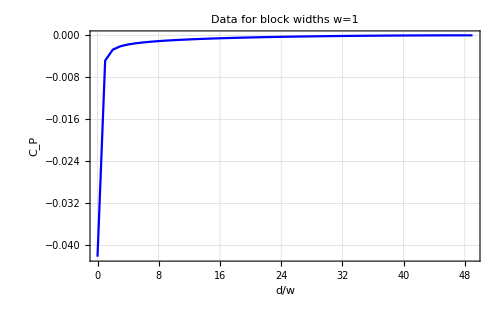

```mathematica
ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPListN100dA1]⟦2⟧}&/@CoPListN100dA1,PlotTheme->"Detailed",PlotStyle->{Blue},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1"]
```

```mathematica
ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPListN100dA1]⟦2⟧}&/@CoPListN100dA1,PlotTheme->"Detailed",PlotStyle->{Blue},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1",PlotLegends->"w=1"]
```

-Graphics-

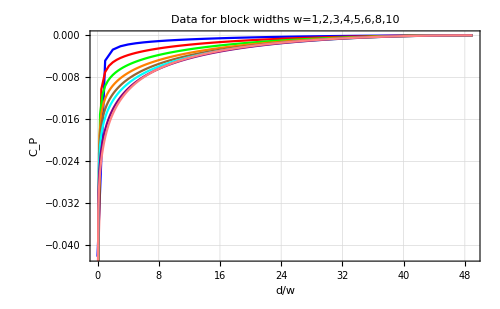

```mathematica
Show[ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPListN100dA1]⟦2⟧}&/@CoPListN100dA1,PlotTheme->"Detailed",PlotStyle->{Blue},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4,5,6,8,10",PlotLegends->Blue"w=1"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPListN200dA2]⟦2⟧}&/@CoPListN200dA2,PlotTheme->"Detailed",PlotStyle->{Red},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Red"w=2"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPListN300dA3]⟦2⟧}&/@CoPListN300dA3,PlotTheme->"Detailed",PlotStyle->{Green},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Green"w=3"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPListN400dA4]⟦2⟧}&/@CoPListN400dA4,PlotTheme->"Detailed",PlotStyle->{Orange},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Orange"w=4"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPListN500dA5]⟦2⟧}&/@CoPListN500dA5,PlotTheme->"Detailed",PlotStyle->{Brown},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Brown"w=5"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPListN600dA6]⟦2⟧}&/@CoPListN600dA6,PlotTheme->"Detailed",PlotStyle->{Cyan},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Cyan"w=6"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPListN800dA8]⟦2⟧}&/@CoPListN800dA8,PlotTheme->"Detailed",PlotStyle->{Purple},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Purple"w=8"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPListN1000dA10]⟦2⟧}&/@CoPListN1000dA10,PlotTheme->"Detailed",PlotStyle->{Pink},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Pink"w=10"]]
```

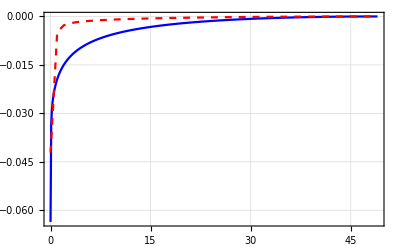

```mathematica
Show[ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPListN1000dA10]⟦2⟧}&/@CoPListN1000dA10,PlotTheme->"Detailed",PlotStyle->{Blue},Joined->True,PlotRange->All],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPListN100dA1]⟦2⟧}&/@CoPListN100dA1,PlotTheme->"Detailed",PlotStyle->{Red,Dashed},Joined->True,PlotRange->All]]
```

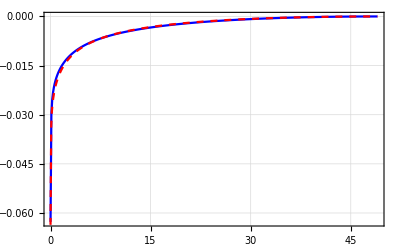

```mathematica
Show[ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPListN800dA8]⟦2⟧}&/@CoPListN800dA8,PlotTheme->"Detailed",PlotStyle->{Blue},Joined->True,PlotRange->All],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPListN1000dA10]⟦2⟧}&/@CoPListN1000dA10,PlotTheme->"Detailed",PlotStyle->{Red,Dashed},Joined->True,PlotRange->All]]
```

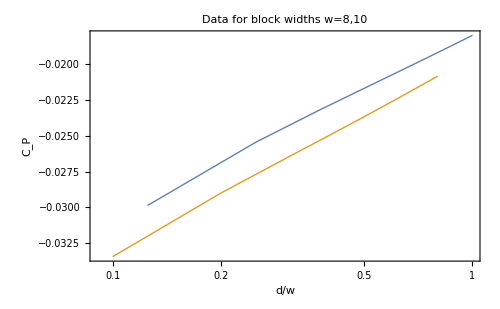

```mathematica
ListLogLinearPlot[{({#⟦1⟧,#⟦2⟧-Last[CoPListN800dA8]⟦2⟧}&/@CoPListN800dA8)⟦1;;9⟧,({#⟦1⟧,#⟦2⟧-Last[CoPListN1000dA10]⟦2⟧}&/@CoPListN1000dA10)⟦1;;9⟧},PlotTheme->"Detailed",Joined->True,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=8,10"]
```

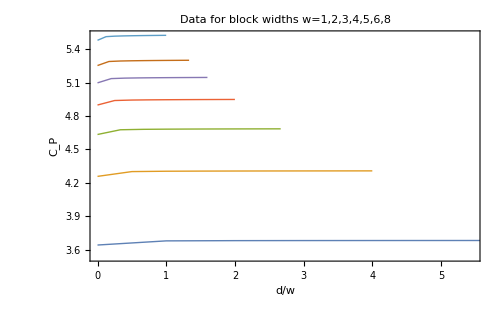

```mathematica
ListPlot[{CoPListN100dA1[[1;;9]],CoPListN200dA2[[1;;9]],CoPListN300dA3[[1;;9]],CoPListN400dA4[[1;;9]],CoPListN500dA5[[1;;9]],CoPListN600dA6[[1;;9]],CoPListN800dA8[[1;;9]]},Joined->True,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4,5,6,8"]
```

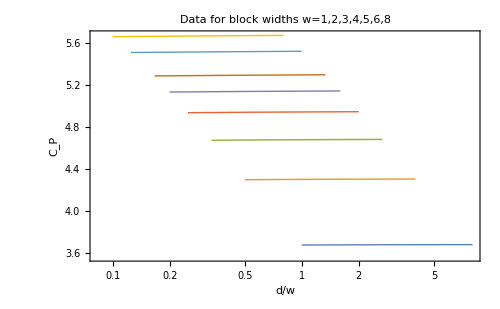

```mathematica
ListLogLinearPlot[{CoPListN100dA1[[1;;9]],CoPListN200dA2[[1;;9]],CoPListN300dA3[[1;;9]],CoPListN400dA4[[1;;9]],CoPListN500dA5[[1;;9]],CoPListN600dA6[[1;;9]],CoPListN800dA8[[1;;9]],CoPListN1000dA10[[1;;9]]},Joined->True,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4,5,6,8"]
```

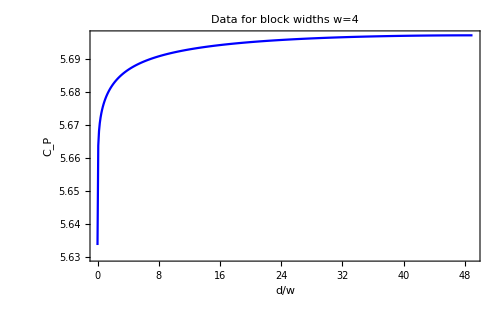

```mathematica
ListPlot[CoPListN1000dA10,PlotRange->Full,Joined->True,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->{Blue},PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=4"]
```

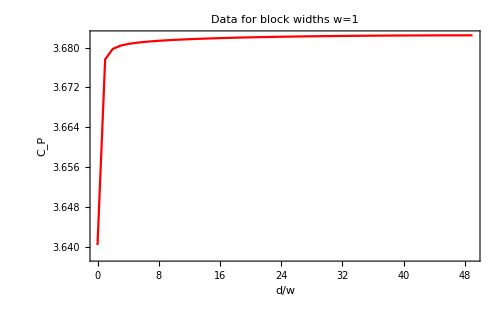

```mathematica
ListPlot[CoPListN100dA1,PlotRange->Full,Joined->True,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->{Red},PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1"]
```

## Entanglement of Purification

### EoP Data

```mathematica
(*EoPListN100dA1=Table[{d,EoPVal[100,1/100,1/100,1,1,1,d]},{d,0,(100-(1+1))/2}]*)
```

```mathematica
EoPListN100dA1={{0,2.601309844110637},{1,2.5335967841594833},{2,2.432702465870051},{3,2.3680368268777556},{4,2.3225378011274316},{5,2.2882023771333486},{6,2.261016502285747},{7,2.238742228381954},{8,2.2200235303207863},{9,2.203984495315874},{10,2.190030302510393},{11,2.1777405228041995},{12,2.1668081249414812},{13,2.157002729501049},{14,2.1481474793681676},{15,2.140103935813631},{16,2.132761899673244},{17,2.126032360634621},{18,2.1198424990245384},{19,2.114132064592227},{20,2.1088507071960985},{21,2.1039559733740054},{22,2.099411783449872},{23,2.0951872555554845},{24,2.0912557876804825},{25,2.087594335300933},{26,2.084182831333538},{27,2.081003725145627},{28,2.0780416034040385},{29,2.0752828831576724},{30,2.0727155588782935},{31,2.0703289899575967},{32,2.068113731210611},{33,2.0660613807827892},{34,2.0641644588592367},{35,2.0624163062110457},{36,2.060810991846105},{37,2.0593432402263443},{38,2.058008367175468},{39,2.0568022249841755},{40,2.0557211562881434},{41,2.05476195418378},{42,2.053921828767759},{43,2.053198378565475},{44,2.052589566814671},{45,2.0520937012863},{46,2.051709418665316},{47,2.0514356712363586},{48,2.051271717429698},{49,2.0512171152430363}};
```

```mathematica
(*EoPListN200dA2=Table[{d/2,EoPVal[200,2/100,1/100,1,2,2,d]},{d,0,(200-(2+2))/2}]*)
```

```mathematica
EoPListN200dA2={{0,2.036487906490735},{1/2,2.0203512258940144},{1,1.8847492273378004},{3/2,1.8157669483281464},{2,1.7671395808669572},{5/2,1.7299389028531493},{3,1.7000687178368208},{7/2,1.675282604080119},{4,1.6542151502117326},{9/2,1.6359761536733601},{5,1.619954435260165},{11/2,1.6057132702229469},{6,1.5929304392779908},{13/2,1.5813618915311731},{7,1.5708186590184494},{15/2,1.5611516971681039},{8,1.5522414849046113},{17/2,1.5439908681869756},{9,1.5363199274639805},{19/2,1.5291619869060629},{10,1.5224612129066806},{21/2,1.5161701914482955},{11,1.5102484355925672},{23/2,1.5046610665309228},{12,1.4993777244082442},{25/2,1.4943722793086625},{13,1.4896215912082769},{27/2,1.4851052481292215},{14,1.4808053367037157},{29/2,1.4767059301025571},{15,1.4727927639587133},{31/2,1.4690528631588888},{16,1.4654746586176293},{33/2,1.4620481758438673},{17,1.4587637534333004},{35/2,1.455612936829837},{18,1.4525879324745492},{37/2,1.4496817747570585},{19,1.446887894602414},{39/2,1.4442004389109084},{20,1.441613826394206},{41/2,1.4391232394453006},{21,1.4367239853825358},{43/2,1.4344117599287476},{22,1.4321826344600979},{45/2,1.4300329129784797},{23,1.42795926203161},{47/2,1.425958500701371},{24,1.4240276505766862},{49/2,1.4221639269464186},{25,1.4203649057662542},{51/2,1.4186280934900701},{26,1.4169512196188512},{53/2,1.4153322983375551},{27,1.413769284433038},{55/2,1.4122603993675424},{28,1.410803791071561},{57/2,1.40939795940408},{29,1.4080413218627794},{59/2,1.4067324221684263},{30,1.4054699515510392},{61/2,1.4042525908505148},{31,1.4030791548281474},{63/2,1.4019485012553867},{32,1.4008595669192745},{65/2,1.3998113402483054},{33,1.3988028541826498},{67/2,1.397833231449948},{34,1.3969016127828375},{69/2,1.3960071954606537},{35,1.3951492181968181},{71/2,1.394326994352544},{36,1.3935398208890684},{73/2,1.3927870605346335},{37,1.3920681491517894},{75/2,1.39138246720348},{38,1.390729561743384},{77/2,1.3901088551134426},{39,1.3895199199927182},{79/2,1.388962318716417},{40,1.388435639355445},{81/2,1.387939499182985},{41,1.3874735029515024},{83/2,1.3870373627209565},{42,1.3866307521567998},{85/2,1.3862533842719507},{43,1.3859049950322397},{87/2,1.3855853492620407},{44,1.3852942277159903},{89/2,1.3850314129739951},{45,1.3847967203414955},{91/2,1.3845900226624426},{46,1.3844111611073864},{93/2,1.384260030367028},{47,1.3841365110499244},{95/2,1.384040521808188},{48,1.3839720060259688},{97/2,1.3839309129890798},{49,1.3839172167830394}};
```

```mathematica
(*EoPListN300dA3=Table[{d/3,EoPVal[300,3/100,1/100,1,3,3,d]},{d,0,(300-(3+3))/2}]*)
```

```mathematica
EoPListN300dA3={{0,1.7250007243055794},{1/3,1.7228495309889689},{2/3,1.578249572518692},{1,1.507662703781879},{4/3,1.4579378570435684},{5/3,1.4196964751936785},{2,1.3887887763672229},{7/3,1.3629748730085391},{8/3,1.3409016401857345},{3,1.3216875876742966},{10/3,1.3047262338931849},{11/3,1.2895826190958113},{4,1.2759344138410498},{13/3,1.2635363368826322},{14/3,1.252197579274668},{5,1.241766928365243},{16/3,1.2321226388664601},{17/3,1.223165298759316},{6,1.214812793908831},{19/3,1.2069965282386799},{20/3,1.199658672880671},{7,1.1927500174374577},{22/3,1.1862284400569536},{23/3,1.1800575445849009},{8,1.1742057302844637},{25/3,1.1686454075868586},{26/3,1.163352308973924},{9,1.1583050389594491},{28/3,1.1534845970009746},{29/3,1.148874087158653},{10,1.144458413833367},{31/3,1.1402239735029498},{32/3,1.1361585218398709},{11,1.1322510829430192},{34/3,1.1284916015489537},{35/3,1.124870997766234},{12,1.1213810225130967},{37/3,1.1180140140374923},{38/3,1.1147631376391454},{13,1.1116218673687657},{40/3,1.1085845081566446},{41/3,1.1056455229806343},{14,1.1028000533788531},{43/3,1.1000433572929456},{44/3,1.0973712563143299},{15,1.0947796774301846},{46/3,1.0922650266545004},{47/3,1.0898237859661721},{16,1.0874527317411773},{49/3,1.0851488627951313},{50/3,1.0829093964882028},{17,1.0807316858192588},{52/3,1.0786132576358698},{53/3,1.0765518271401984},{18,1.0745451441127303},{55/3,1.072591160250674},{56/3,1.070688046755555},{19,1.0688338476870096},{58/3,1.0670269026054446},{59/3,1.065265604345735},{20,1.0635483977023754},{61/3,1.0618737557767484},{62/3,1.060240366299182},{21,1.0586468827527282},{64/3,1.0570921140686347},{65/3,1.0555748094575752},{22,1.0540939198863462},{67/3,1.0526483670182727},{68/3,1.0512370385893803},{23,1.0498590771094163},{70/3,1.0485134944063421},{71/3,1.0471994485090943},{24,1.045916141991628},{73/3,1.0446626588489414},{74/3,1.0434382525678416},{25,1.0422422775189408},{76/3,1.041074030851476},{77/3,1.039932730304402},{26,1.0388178469495113},{79/3,1.0377287236315043},{80/3,1.0366648182878813},{27,1.03562544789883},{82/3,1.0346102224328046},{83/3,1.0336185207217947},{28,1.0326498746969868},{85/3,1.0317038410304926},{86/3,1.03077991884116},{29,1.029877711118325},{88/3,1.0289967501393145},{89/3,1.0281366496573212},{30,1.0272970440070628},{91/3,1.02647756179703},{92/3,1.0256777499114267},{31,1.0248973721868526},{94/3,1.0241360777905504},{95/3,1.0233935225121935},{32,1.0226693816149086},{97/3,1.0219633985546168},{98/3,1.0212752609077462},{33,1.0206047065108397},{100/3,1.0199514711996807},{101/3,1.0193153077872268},{34,1.0186959704253693},{103/3,1.0180932093109263},{104/3,1.017506802383717},{35,1.016936542093292},{106/3,1.01638223432893},{107/3,1.015843627044975},{36,1.0153205599875683},{109/3,1.01481286149168},{110/3,1.014320325318462},{37,1.0138427960661245},{112/3,1.013380103754809},{113/3,1.012932094442361},{38,1.012498599355054},{115/3,1.0120794942399058},{116/3,1.0116746211936762},{39,1.0112838628527354},{118/3,1.0109070728333867},{119/3,1.0105441285434917},{40,1.0101949371884107},{121/3,1.0098593602806942},{122/3,1.0095373020677556},{41,1.0092286649857274},{124/3,1.0089333186110725},{125/3,1.0086512180749188},{42,1.0083822422656148},{127/3,1.0081263119100332},{128/3,1.0078833588182046},{43,1.0076533027587131},{130/3,1.0074360785612488},{131/3,1.007231605531991},{44,1.007039827417668},{133/3,1.0068607035882793},{134/3,1.0066941479035068},{45,1.0065401405296273},{136/3,1.0063986202313213},{137/3,1.0062695422594488},{46,1.0061528773495407},{139/3,1.0060485766833462},{140/3,1.0059566290792015},{47,1.0058769879188847},{142/3,1.0058096434334818},{143/3,1.005754567084118},{48,1.0057117474391912},{145/3,1.0056811764796714},{146/3,1.0056628305247122},{49,1.0056567169142987}};
```

```mathematica
(*EoPListN400dA4=Table[{d/4,EoPVal[400,4/100,1/100,1,4,4,d]},{d,0,(400-(4+4))/2}]*)
```

```mathematica
EoPListN400dA4={{0,1.5215708447859468},{1/4,1.5236947444806273},{1/2,1.376688661011247},{3/4,1.3052971650015563},{1,1.2550201812020538},{5/4,1.2162517269844935},{3/2,1.184803804054316},{7/4,1.1584364033326022},{2,1.1358037352192105},{9/4,1.1160318222278267},{5/2,1.0985197933464943},{11/4,1.0828365170493703},{3,1.0686621872568332},{13/4,1.0557528585613443},{7/2,1.0439183180076768},{15/4,1.0330075097179154},{4,1.0228984886656671},{17/4,1.0134913819355424},{9/2,1.0047034958572174},{19/4,0.9964655967800757},{5,0.9887191514056846},{21/4,0.9814142974199087},{11/2,0.9745081206374584},{23/4,0.9679636454280971},{6,0.9617485311580125},{25/4,0.955834639948598},{13/2,0.9501970657707312},{27/4,0.9448138771158059},{7,0.9396655532385866},{29/4,0.9347347431174131},{15/2,0.930005723466363},{31/4,0.9254646064976706},{8,0.9210987440582757},{33/4,0.9168966602852813},{17/2,0.9128480250286974},{35/4,0.9089433972388096},{9,0.9051741655758541},{37/4,0.9015324572957174},{19/2,0.8980110463803701},{39/4,0.8946033147737558},{10,0.8913031261680184},{41/4,0.8881048630021029},{21/2,0.8850033371496411},{43/4,0.881993651358897},{11,0.8790713685519793},{45/4,0.876232331701876},{23/2,0.873472661869063},{47/4,0.8707887234904225},{12,0.8681771625610883},{49/4,0.8656348131418181},{25/2,0.8631587254289614},{51/4,0.8607461331377319},{13,0.8583944356798621},{53/4,0.856101159738005},{27/2,0.8538640543421627},{55/4,0.851680926385755},{14,0.8495497656828335},{57/4,0.8474685510338458},{29/2,0.8454355171637701},{59/4,0.8434489760940704},{15,0.8415072627371833},{61/4,0.8396088266808218},{31/2,0.8377522306445067},{63/4,0.8359360395051346},{16,0.83415905520415},{65/4,0.832419783922989},{33/2,0.830717258210655},{67/4,0.829050140477184},{17,0.8274175411309738},{69/4,0.8258183202996414},{35/2,0.8242515562581508},{71/4,0.8227162479836453},{18,0.8212114465153648},{73/4,0.8197363978685992},{37/2,0.8182902718905734},{75/4,0.8168721946435991},{19,0.8154814614851569},{77/4,0.8141174163935452},{39/2,0.812779263704472},{79/4,0.8114664342426807},{20,0.810178152886722},{81/4,0.8089139504302008},{41/2,0.8076731801276136},{83/4,0.8064552989595679},{21,0.8052597366073376},{85/4,0.8040859464921791},{43/2,0.8029335144086567},{87/4,0.8018018690636763},{22,0.800690558384323},{89/4,0.7995992210610587},{45/2,0.7985273388384126},{91/4,0.7974745110370318},{23,0.7964403695784168},{93/4,0.7954244628602198},{47/2,0.7944265068815493},{95/4,0.7934460800026214},{24,0.7924828207985712},{97/4,0.7915364447911194},{49/2,0.7906066183782063},{99/4,0.7896928983920644},{25,0.7887951551665369},{101/4,0.7879130620373025},{51/2,0.7870462825378591},{103/4,0.7861945931777242},{26,0.785357685144368},{105/4,0.7845352851188915},{53/2,0.7837271757816625},{107/4,0.7829331488546576},{27,0.7821528901231425},{109/4,0.7813862701166703},{55/2,0.780632928061202},{111/4,0.779892827960336},{28,0.7791656330690875},{113/4,0.7784511801012395},{57/2,0.7777493045706793},{115/4,0.7770597998802516},{29,0.7763824855223467},{117/4,0.7757171196283816},{59/2,0.7750636031011217},{119/4,0.7744217643668011},{30,0.7737914133550966},{121/4,0.7731724393373095},{61/2,0.7725646370777788},{123/4,0.7719678749605448},{31,0.7713820360871105},{125/4,0.7708069390720058},{63/2,0.7702424939419884},{127/4,0.7696885417460857},{32,0.7691449388419906},{129/4,0.7686115574915637},{65/2,0.7680883238557005},{131/4,0.7675750803744843},{33,0.7670717469338197},{133/4,0.7665781883410937},{67/2,0.7660942690538928},{135/4,0.7656199457492656},{34,0.7651550702491873},{137/4,0.7646995645085541},{69/2,0.7642533283511684},{139/4,0.7638162810664759},{35,0.7633882943431968},{141/4,0.7629693099260504},{71/2,0.7625592523712187},{143/4,0.7621580152120809},{36,0.7617655397166609},{145/4,0.7613817150697614},{73/2,0.76100648391413},{147/4,0.7606397730199783},{37,0.7602815260500473},{149/4,0.7599316463359781},{75/2,0.7595900843216743},{151/4,0.7592567539760959},{38,0.758931623958073},{153/4,0.7586146033579501},{77/2,0.7583056602491192},{155/4,0.7580046974391221},{39,0.7577116985660226},{157/4,0.7574265950887179},{79/2,0.7571493363571419},{159/4,0.7568798469937243},{40,0.7566181257480622},{161/4,0.7563640945259545},{81/2,0.7561176933499038},{163/4,0.7558789084261214},{41,0.7556476857879326},{165/4,0.7554240252799305},{83/2,0.7552077661660134},{167/4,0.7549989985636494},{42,0.7547976370744137},{169/4,0.7546036416752827},{85/2,0.7544169762907766},{171/4,0.7542376225239034},{43,0.7540655582259935},{173/4,0.7539007219126308},{87/2,0.7537431108299},{175/4,0.753592701599346},{44,0.7534494327081048},{177/4,0.7533133105020595},{89/2,0.7531843108995416},{179/4,0.7530624095442846},{45,0.7529475697663739},{181/4,0.75283979388274},{91/2,0.7527390612953765},{183/4,0.7526453463139327},{46,0.7525586343513424},{185/4,0.7524789081790906},{93/2,0.7524061599083564},{187/4,0.7523403753509283},{47,0.7522815533970325},{189/4,0.7522296556703726},{95/2,0.7521847162000685},{191/4,0.7521466873051712},{48,0.7521155865757658},{193/4,0.7520914094631195},{97/2,0.7520741293423031},{195/4,0.7520637690118086},{49,0.7520603235738328}};
```

```mathematica
(*EoPListN500dA5=Table[{d/5,EoPVal[500,5/100,1/100,1,5,5,d]},{d,0,(500-(5+5))/2}]*)
```

```mathematica
EoPListN500dA5={{0,1.3793238796724894},{1/5,1.4197043758432932},{2/5,1.2351470157069206},{3/5,1.1632936554193092},{4/5,1.1126866226306353},{1,1.0736026933046925},{6/5,1.0418276163375046},{7/5,1.0151189206832731},{8/5,0.9921345391438189},{9/5,0.9720051049660711},{2,0.9541338638455699},{11/5,0.9380931624388886},{12/5,0.9235654553325318},{13/5,0.9103086354044058},{14/5,0.8981336925220276},{3,0.8868901591680544},{16/5,0.8764565764495443},{17/5,0.8667333616038604},{18/5,0.8576377737389498},{19/5,0.8491005418680063},{4,0.8410627888503188},{21/5,0.8334745902924772},{22/5,0.8262927894209294},{23/5,0.8194799517994696},{24/5,0.8130036355174474},{5,0.8068351844275137},{26/5,0.8009495469359279},{27/5,0.7953244600277052},{28/5,0.7899400733920678},{29/5,0.7847786927863672},{6,0.7798245421534907},{31/5,0.7750631793437698},{32/5,0.7704819724351671},{33/5,0.7660690480305682},{34/5,0.7618138572118855},{7,0.7577068622873093},{36/5,0.7537390743246296},{37/5,0.7499025514208737},{38/5,0.7461899201411503},{39/5,0.7425942542459877},{8,0.7391093353756863},{41/5,0.7357293775916522},{42/5,0.7324490056898005},{43/5,0.7292632285241614},{44/5,0.7261674667290277},{9,0.7231574291966522},{46/5,0.7202290921536789},{47/5,0.7173787083438936},{48/5,0.7146028611348174},{49/5,0.7118982495095327},{10,0.7092617822958212},{51/5,0.7066906677522987},{52/5,0.7041821490453072},{53/5,0.7017337391989451},{54/5,0.6993430568713095},{11,0.697007856595087},{56/5,0.6947259683664655},{57/5,0.6924954222472813},{58/5,0.6903143481061502},{59/5,0.6881809698691637},{12,0.6860935337892377},{61/5,0.6840504671962266},{62/5,0.6820502606923288},{63/5,0.6800914314561959},{64/5,0.6781726409843029},{13,0.6762925822868417},{66/5,0.674449947139965},{67/5,0.6726436204249833},{68/5,0.6708725380583606},{69/5,0.6691353612281832},{14,0.6674312546977506},{71/5,0.6657592691239633},{72/5,0.6641184086196569},{73/5,0.66250778457973},{74/5,0.6609265270856151},{15,0.6593737691527605},{76/5,0.6578487426653833},{77/5,0.6563507504189939},{78/5,0.6548791749740833},{79/5,0.6534329545248769},{16,0.6520117040440694},{81/5,0.6506147728691966},{82/5,0.6492414911688729},{83/5,0.6478912537014017},{84/5,0.6465635183361167},{17,0.6452577757984703},{86/5,0.6439734505532805},{87/5,0.6427099065694101},{88/5,0.6414668471777945},{89/5,0.6402437792787683},{18,0.6390403544364027},{91/5,0.6378556736043414},{92/5,0.6366897832888404},{93/5,0.6355420542415408},{94/5,0.6344122246977526},{19,0.6332997986408855},{96/5,0.6322044593507037},{97/5,0.6311259167507658},{98/5,0.6300635735806249},{99/5,0.6290174085361028},{20,0.6279869420864128},{101/5,0.626971841638917},{102/5,0.6259719071593474},{103/5,0.6249867987871283},{104/5,0.6240161131718223},{21,0.623059786452872},{106/5,0.6221173839285823},{107/5,0.6211887128434858},{108/5,0.6202735184507129},{109/5,0.6193716014459899},{22,0.6184826408158192},{111/5,0.6176064791247443},{112/5,0.6167428441725196},{113/5,0.6158915674049381},{114/5,0.6150523484089118},{23,0.6142251335735058},{116/5,0.6134096201931474},{117/5,0.6126056144792549},{118/5,0.6118129289441057},{119/5,0.6110314963639791},{24,0.6102609154088281},{121/5,0.6095011916385142},{122/5,0.6087521706358969},{123/5,0.6080135629557775},{124/5,0.6072852910981517},{25,0.6065672137743089},{126/5,0.605859129810125},{127/5,0.605160897135411},{128/5,0.604472445107531},{129/5,0.6037935516810007},{26,0.6031242104204544},{131/5,0.6024639919102703},{132/5,0.6018130839308813},{133/5,0.6011712271653333},{134/5,0.6005383232636129},{27,0.5999142277832337},{136/5,0.599298930853489},{137/5,0.5986921008950038},{138/5,0.5980938521687467},{139/5,0.5975039763034976},{28,0.5969223705982545},{141/5,0.5963489123135071},{142/5,0.5957835331567338},{143/5,0.5952261944702506},{144/5,0.5946766421088551},{29,0.5941349237276803},{146/5,0.5936009087780312},{147/5,0.5930744912925529},{148/5,0.5925555895425976},{149/5,0.5920441463035251},{30,0.5915400509976043},{151/5,0.5910432339073528},{152/5,0.590553606011113},{153/5,0.5900711394551225},{154/5,0.5895956407032019},{31,0.589127156835313},{156/5,0.5886655634654224},{157/5,0.5882108323391755},{158/5,0.587762823816314},{159/5,0.587321522500548},{32,0.586886864318118},{161/5,0.5864587212389707},{162/5,0.5860371579003385},{163/5,0.585622013137808},{164/5,0.585213223365638},{33,0.5848107748685099},{166/5,0.584414626345896},{167/5,0.5840246383168587},{168/5,0.5836408336737843},{169/5,0.5832631299375253},{34,0.5828915013577509},{171/5,0.5825258418529642},{172/5,0.5821661729109853},{173/5,0.581812380482932},{174/5,0.5814644562227039},{35,0.5811223822534076},{176/5,0.580786007523941},{177/5,0.5804553913348279},{178/5,0.5801304565202763},{179/5,0.5798111496335536},{36,0.5794974608093783},{181/5,0.5791893181299614},{182/5,0.5788866868847309},{183/5,0.5785895198658572},{184/5,0.5782978312754239},{37,0.5780115283027913},{186/5,0.5777306220332026},{187/5,0.5774549923427597},{188/5,0.5771847290452321},{189/5,0.5769197062140474},{38,0.576659922446887},{191/5,0.5764053487803827},{192/5,0.5761559701892962},{193/5,0.5759116809639447},{194/5,0.5756725428593115},{39,0.5754384861100437},{196/5,0.5752094823967268},{197/5,0.5749855252982388},{198/5,0.5747665794938188},{199/5,0.5745525808231107},{40,0.5743435552115892},{201/5,0.5741394752147793},{202/5,0.5739402906291197},{203/5,0.573745991578333},{204/5,0.5735565566478038},{41,0.573371959939973},{206/5,0.5731922050647588},{207/5,0.5730172124144315},{208/5,0.5728470256364443},{209/5,0.5726815781323851},{42,0.5725208926889123},{211/5,0.5723649279122461},{212/5,0.5722136617103419},{213/5,0.5720670939116382},{214/5,0.5719252192979806},{43,0.571787943696326},{216/5,0.5716553564089414},{217/5,0.5715273870523307},{218/5,0.5714040317250917},{219/5,0.5712852747237227},{44,0.571171103793459},{221/5,0.5710615230717581},{222/5,0.5709564934816537},{223/5,0.5708560115850008},{224/5,0.570760085144224},{45,0.5706686719484979},{226/5,0.5705817962742844},{227/5,0.5704994127282932},{228/5,0.5704215470072176},{229/5,0.570348172402704},{46,0.5702793109441306},{231/5,0.5702148660231147},{232/5,0.5701549274482146},{233/5,0.5700994684869534},{234/5,0.5700484505279076},{47,0.5700018849162858},{236/5,0.5699597673048628},{237/5,0.5699221013391166},{238/5,0.5698888862473126},{239/5,0.5698600919629225},{48,0.5698357349714828},{241/5,0.5698158078778922},{242/5,0.5698003273747174},{243/5,0.5697892629816659},{244/5,0.5697826142262798},{49,0.5697804031822358}};
```

```mathematica
(*EoPListN600dA6=Table[{d/6,EoPVal[600,6/100,1/100,1,6,6,d]},{d,0,(600-(6+6))/2}]*)
```

```mathematica
EoPListN600dA6=;
```

```mathematica
(*EoPListN800dA8=Table[{d/8,EoPVal[800,8/100,1/100,1,8,8,d]},{d,0,(800-(8+8))/2}]*)
```

```mathematica
EoPListN800dA8=;
```

```mathematica
(*EoPListN1000dA10=Table[{d/10,EoPVal[1000,10/100,1/100,1,10,10,d]},{d,0,(1000-(10+10))/2}]*)
```

```mathematica
EoPListN1000dA10=;
```

### EoP Plots

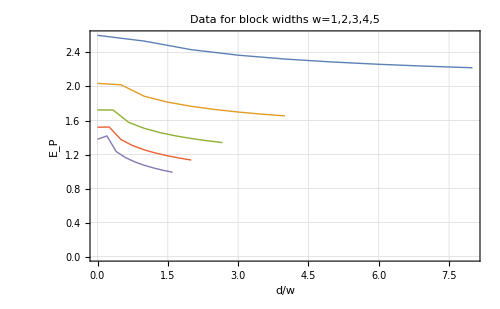

```mathematica
ListPlot[{EoPListN100dA1⟦1;;9⟧,EoPListN200dA2⟦1;;9⟧,EoPListN300dA3⟦1;;9⟧,EoPListN400dA4⟦1;;9⟧,EoPListN500dA5⟦1;;9⟧},PlotTheme->"Detailed" ,Joined->True,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "E_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4,5"]
```

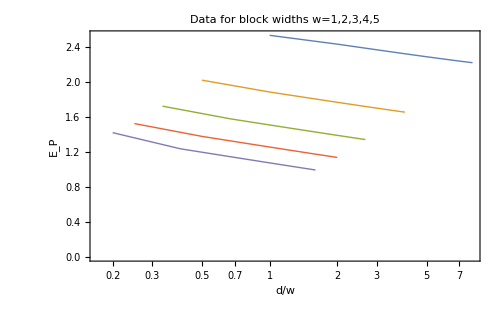

```mathematica
ListLogLinearPlot[{EoPListN100dA1⟦1;;9⟧,EoPListN200dA2⟦1;;9⟧,EoPListN300dA3⟦1;;9⟧,EoPListN400dA4⟦1;;9⟧,EoPListN500dA5⟦1;;9⟧},PlotTheme->"Detailed" ,Joined->True,PlotMarkers->None,Axes->False,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "E_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4,5"]
```

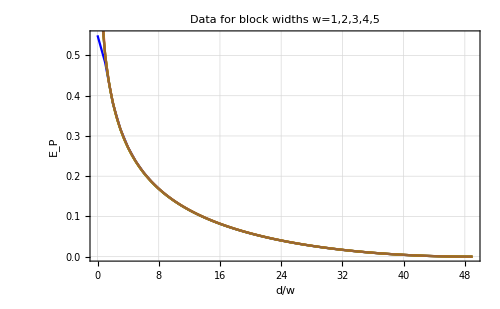

```mathematica
Show[ListPlot[{#⟦1⟧,#⟦2⟧-Last[EoPListN100dA1]⟦2⟧}&/@EoPListN100dA1,PlotTheme->"Detailed",PlotStyle->{Blue},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "E_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4,5",PlotLegends->Blue"w=1"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[EoPListN200dA2]⟦2⟧}&/@EoPListN200dA2,PlotTheme->"Detailed",PlotStyle->{Red},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "E_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Red"w=2"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[EoPListN300dA3]⟦2⟧}&/@EoPListN300dA3,PlotTheme->"Detailed",PlotStyle->{Green},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "E_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Green"w=3"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[EoPListN400dA4]⟦2⟧}&/@EoPListN400dA4,PlotTheme->"Detailed",PlotStyle->{Orange},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "E_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Orange"w=4"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[EoPListN500dA5]⟦2⟧}&/@EoPListN500dA5,PlotTheme->"Detailed",PlotStyle->{Brown},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "E_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Brown"w=5"]]
```

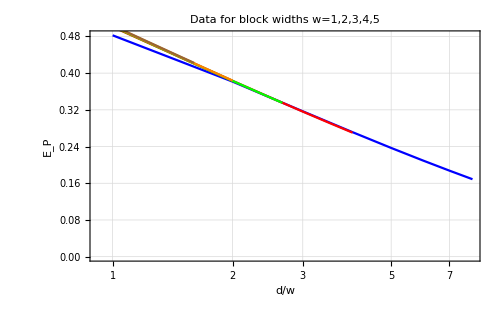

```mathematica
Show[ListLogLinearPlot[({#⟦1⟧,#⟦2⟧-Last[EoPListN100dA1]⟦2⟧}&/@EoPListN100dA1)⟦1;;9⟧,PlotTheme->"Detailed",PlotStyle->{Blue},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "E_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4,5",PlotLegends->Blue"w=1"],ListLogLinearPlot[({#⟦1⟧,#⟦2⟧-Last[EoPListN200dA2]⟦2⟧}&/@EoPListN200dA2)⟦1;;9⟧,PlotTheme->"Detailed",PlotStyle->{Red},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "E_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Red"w=2"],ListLogLinearPlot[({#⟦1⟧,#⟦2⟧-Last[EoPListN300dA3]⟦2⟧}&/@EoPListN300dA3)⟦1;;9⟧,PlotTheme->"Detailed",PlotStyle->{Green},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "E_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Green"w=3"],ListLogLinearPlot[({#⟦1⟧,#⟦2⟧-Last[EoPListN400dA4]⟦2⟧}&/@EoPListN400dA4)⟦1;;9⟧,PlotTheme->"Detailed",PlotStyle->{Orange},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "E_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Orange"w=4"],ListLogLinearPlot[({#⟦1⟧,#⟦2⟧-Last[EoPListN500dA5]⟦2⟧}&/@EoPListN500dA5)⟦1;;9⟧,PlotTheme->"Detailed",PlotStyle->{Brown},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "E_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Brown"w=5"]]
```